# Genetic signatures of evolutionary rescue by a selective sweep

## Matthew M Osmond & Graham Coop

Center for Population Biology and Department of Evolution and Ecology, University of California - Davis

mmosmond@ucdavis.edu

## Dependencies

### Directories

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
imagedir="../figures/";(*where to save images*)
datadir="simulations/";(*where simulation data is*)
```

### Plotting functions

#### Style

```mathematica
defaultcolors=ColorData[1,"ColorList"];(*colors*)
labelstyle=Directive[FontSize->12,FontFamily->"Helvetica"];(*font for axis labels*)
letterstyle=Directive[FontSize->14,FontFamily->"Helvetica"];(*font for panel letters*)
letterposition={0.05,0.925};(*position of panel letters*)
padding={{60,10},{40,10}};(*padding around figures*)
Hpadding={{70,10},{40,10}};(*special case of padding for diversity plots*)
ylabelposition={-0.15,0.5};(*position of y-axis labels*)
Needs["ErrorBarPlots`"];(*for plotting error bars*)
```

#### Forward-time dynamics

For plots of allele frequency and population size, forward in time

```mathematica
plotDynamics[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_,maxt_, letter_]:=

(
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval};

topstyle=Which[
letter=="A",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Rotate[Text[Style["Allele frequency",labelstyle],Scaled@ylabelposition],π/2],
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="C",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Rotate[Text[Style["Allele frequency",labelstyle],Scaled@ylabelposition],π/2],
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="D",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
}
];
bottomstyle=Which[
letter=="A",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Rotate[Text[Style["Population size",labelstyle],Scaled@ylabelposition],π/2]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic}
},
letter=="C",
{
FrameTicksStyle->{Automatic,Automatic,Automatic,Automatic},
Epilog->{
Rotate[Text[Style["Population size",labelstyle],Scaled@ylabelposition],π/2]
},
FrameLabel->{"Generation"}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Generation"}
}
];

(*rescue: simulations*)
folder=StringForm["rescue_N``_d``_s``_h``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],NumberForm[hval,{2,1}],kval,NumberForm[uval,{6,5}],If[0<mval<1,NumberForm[mval,{3,2}],mval]];
Clear[data]
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/dynamics_"<>ToString[i-1]<>".txt", "Table", "FieldSeparators"->" "],{i,nreps}];
allp=Table[data[i][[2;;,3]],{i,nreps}];
alln=Table[data[i][[2;;,2]],{i,nreps}];
allppadded=PadRight[allp-1]+1;
allnpadded=PadRight[alln-N0]+N0/.params;
medp=Median/@Table[allppadded[[All,i]],{i,Length[allppadded[[1]]]}];
medn=Median/@Table[allnpadded[[All,i]],{i,Length[allnpadded[[1]]]}];

(*constant: simulations*)
folder=StringForm["rescue_N``_d0.00_s``_h``_k``_u``_m``",Nval,NumberForm[sval,{3,2}],NumberForm[hval,{2,1}],kval,NumberForm[uval,{6,5}],If[0<mval<1,NumberForm[mval,{3,2}],mval]];
Clear[data]
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/dynamics_"<>ToString[i-1]<>".txt", "Table", "FieldSeparators"->" "],{i,nreps}];
sweepallp=Table[data[i][[2;;,3]],{i,nreps}];
sweepalln=Table[data[i][[2;;,2]],{i,nreps}];
sweepallppadded=PadRight[sweepallp-1]+1;
sweepallnpadded=PadRight[sweepalln-N0]+N0/.params;
sweepmedp=Median/@Table[sweepallppadded[[All,i]],{i,Length[sweepallppadded[[1]]]}];
sweepmedn=Median/@Table[sweepallnpadded[[All,i]],{i,Length[sweepallnpadded[[1]]]}];

(*rescue: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]]/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.B->2;
numerics=RecurrenceTable[{n[t+1]== Min[n[t] wbar,N0],q[t+1]==qnew,n[0]==N0,q[0]==q0}/.params,{n,q},{t,0,maxt}];
theoryq= q[t]/.qtadditive/.params;
theoryn= Min[Re[n[t]],N0]/.ntadditive/.params;

(*constant: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)/.B->2;(*rescue lifecycle*)
(*q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.p->pest/.v->1/.w->1+s h;(*WF*)*)
numericssweep=RecurrenceTable[{q[t+1]==qnew,q[0]==q0}/.params,q,{t,0,maxt}];
theoryqsweep=q[t]/.qtadditive/.params;

(*PANEL A: ALLELE FREQUENCY DYNAMICS*)
pt=Show[
ListPlot[
 allp,
Joined->True,
PlotStyle->Directive[defaultcolors[[1]],Thickness[0.002],Opacity[0.2]]
],
ListPlot[
numericssweep,
Joined->True,
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[3]]
],
Plot[
theoryqsweep,{t,0,maxt},
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[3],Dashing[Medium]]
],
ListPlot[
numerics[[All,2]],
Joined->True,
PlotStyle->Directive[AbsoluteThickness[3]]
],
Plot[
theoryq,{t,0,maxt},
PlotStyle->Directive[AbsoluteThickness[3],Dashing[Medium]]
],
ListPlot[
sweepmedp,
Joined->True,
PlotStyle->Directive[defaultcolors[[2]],Thickness[0.005],Opacity[0.8]]
],
ListPlot[
medp,
Joined->True,
PlotStyle->Directive[defaultcolors[[1]],Thickness[0.005],Opacity[0.8]]
],
PlotRange->{{0,maxt},{0,1.01}},
Frame->{True,True,False,False},
FrameStyle->labelstyle,
PlotRangePadding->None,
ImagePadding->padding,
PlotRangeClipping->False,
topstyle
];
Export[imagedir<>ToString[StringForm["pt_rescue_s``_k``_u``_m``.pdf",sval,kval,uval,mval]],pt];

(*PANEL B: POPULATION DYNAMICS*)
nt=Show[
ListPlot[
 alln,
Joined->True,
PlotStyle->Directive[defaultcolors[[1]],Thickness[0.002],Opacity[0.2]]
],
ListPlot[
{numerics[[All,1]]},
Joined->True,
PlotStyle->Directive[AbsoluteThickness[3]]
],
Plot[
{theoryn},{t,0,maxt},
PlotStyle->Directive[AbsoluteThickness[3],Dashing[Medium]]
],
ListPlot[
sweepmedn,
Joined->True,
PlotStyle->Directive[defaultcolors[[2]],Thickness[0.005],Opacity[0.8]]
],
ListPlot[
medn,
Joined->True,
PlotStyle->Directive[defaultcolors[[1]],Thickness[0.005],Opacity[0.8]]
],
PlotRange->{{0,maxt},{0,Nval*1.01}},
Frame->{True,True,False,False},
FrameStyle->labelstyle,
PlotRangePadding->None,
ImagePadding->padding,
PlotRangeClipping->False,
bottomstyle
];
Export[imagedir<>ToString[StringForm["nt_rescue_s``_k``_u``_m``.pdf",sval,kval,uval,mval]],nt];

Clear[q0];
GraphicsColumn[{pt,nt},ImageSize->400,Spacings->0]
)
```

#### Forward time dynamics, logged

Plots allele frequency dynamics on a log scale (to see accuracy of approximations)

```mathematica
plotDynamicsLog[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_,maxt_]:=

(
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval};
caption=
If[kval>0,StringForm["κ=``\ns=``",kval,sval],
If[uval>0,StringForm["u=``\ns=``",ScientificForm[uval,1],sval],
StringForm["m=``\ns=``",mval,sval]
]
];

(*rescue: simulations*)
folder=StringForm["rescue_N``_d``_s``_h``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],NumberForm[hval,{2,1}],kval,NumberForm[uval,{6,5}],If[0<mval<1,NumberForm[mval,{3,2}],mval]];
Clear[data]
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/dynamics_"<>ToString[i-1]<>".txt", "Table", "FieldSeparators"->" "],{i,nreps}];
allp=Table[data[i][[2;;,3]],{i,nreps}];
allppadded=PadRight[allp-1]+1;
medp=Median/@Table[allppadded[[All,i]],{i,Length[allppadded[[1]]]}];

(*rescue: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]]/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.B->2;
numerics=RecurrenceTable[{n[t+1]== Min[n[t] wbar,N0],q[t+1]==qnew,n[0]==N0,q[0]==q0}/.params,{n,q},{t,0,maxt}];
theoryq= q[t]/.qtadditive/.params;
theoryn= Min[Re[n[t]],N0]/.ntadditive/.params;

(*constant: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)/.B->2;(*same probability of establishment as rescue*)
(*q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.p->pest/.v->1/.w->(1+s h);(*same probability of establishment as WF*)*)
numericssweep=RecurrenceTable[{q[t+1]==qnew,q[0]==q0}/.params,q,{t,0,maxt}];
theoryqsweep=q[t]/.qtadditive/.params;

(*PANEL A: ALLELE FREQUENCY DYNAMICS*)
pt=Show[
ListLogPlot[
 allp,
Joined->True,
PlotStyle->Directive[defaultcolors[[1]],Thickness[0.002],Opacity[0.2]],
PlotRange->{{0,maxt},{1/(2N0)/.params,1.01}}
],
ListLogPlot[
medp,
Joined->True,
PlotStyle->Directive[defaultcolors[[3]],AbsoluteThickness[3],Opacity[0.8]],
Axes->False,
PlotRange->{{0,maxt},{1/(2N0)/.params,1.01}},
PlotLegends->Placed[LineLegend[Style[#,labelstyle]&/@{"simulation median"}],Scaled@{0.75,0.3}]
],
ListLogPlot[
numericssweep,
Joined->True,
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[3]],
PlotLegends->Placed[LineLegend[Style[#,labelstyle]&/@{"constant N (eq 3)"}],Scaled@{0.75,0.4}],
Axes->False,
PlotRange->{{0,maxt},{1/(2N0)/.params,1.01}}
],
LogPlot[
theoryqsweep,{t,0,maxt},
PlotStyle->Directive[defaultcolors[[2]],AbsoluteThickness[3],Dashing[Medium]],
PlotLegends->Placed[LineLegend[Style[#,labelstyle]&/@{"constant N (eq 4)"}],Scaled@{0.75,0.5}],
Axes->False,
PlotRange->{{0,maxt},{1/(2N0)/.params,1.01}}
],
ListLogPlot[
numerics[[All,2]],
Joined->True,
PlotStyle->Directive[AbsoluteThickness[3]],
PlotLegends->Placed[LineLegend[Style[#,labelstyle]&/@{"rescue (eq 3)"}],Scaled@{0.75,0.6}],
Axes->False,
PlotRange->{{0,maxt},{1/(2N0)/.params,1.01}}
],
LogPlot[
theoryq,{t,0,maxt},
PlotStyle->Directive[AbsoluteThickness[3],Dashing[Medium]],
PlotLegends->Placed[LineLegend[Style[#,labelstyle]&/@{"rescue (eq 4)"}],Scaled@{0.75,0.7}],
Axes->False,
PlotRange->{{0,maxt},{1/(2N0)/.params,1.01}}
],
PlotRange->{{0,maxt},Log@{1/(2N0)/.params,1.01}},
Frame->{True,True,False,False},
FrameStyle->labelstyle,
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
PlotRangePadding->None,
ImagePadding->padding,
PlotRangeClipping->False,
Epilog->{
Rotate[Text[Style["Allele frequency",labelstyle],Scaled@ylabelposition],π/2],
Text[Style[caption,letterstyle],Scaled@{0.9,0.1}]
}
];

Clear[q0];
GraphicsColumn[{pt},ImageSize->400,Spacings->-50]
)
```

#### Coalescent

Plot timing of events backwards in time

```mathematica
plotCoalescent[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,lval_,rval_,maxt_,ymax_,NeNval_,NeNcval_,letter_]:=
(
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval,l->lval,r->rval,NeN->NeNval,NeNc->NeNcval};

ticks={Table[{-x,x},{x,0,maxt,50}],Automatic,None,None};
topstyle=Which[
letter=="A",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="C",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="D",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
}
];
bottomstyle=Which[
letter=="A",
{
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Rotate[Text[Style["Probability",labelstyle],Scaled@ylabelposition],π/2]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic}
},
letter=="C",
{
FrameTicksStyle->{Automatic,Automatic,Automatic,Automatic},
Epilog->{
Rotate[Text[Style["Probability",labelstyle],Scaled@ylabelposition],π/2]
},
FrameLabel->{"Generations before fixation"}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Generations before fixation"}
}
];

(*rescue: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]]/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.B->2;
nsol=n[t_]->Min[Re[ntadditiveback[t]],N0];
xsol=x[t_]->qtadditiveback[t];
tmax=Re[tfixadditive/.params];
tmaxrescue=tmax;
nothingyet[l_,τ_]:=
Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]-migbackapprox[l,τ]];
rescuecoal=Table[{-τ,Re[pcoal[l,τ]nothingyet[l,τ]/.ne[t_]->n[t]NeN/.xsol/.nsol/.params]},{τ,0,tmax}];
rescuerec=Table[{-τ,Re[preco[l,τ]nothingyet[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];
rescuemut=Table[{-τ,Re[pmut[l,τ]nothingyet[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];
rescuemig=Table[{-τ,Re[pmig[l,τ]nothingyet[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];
rescuen=Table[{-t,n[tmax-t]/.nsol/.params},{t,0,tmax}];
rescuep=Table[{-t,N0 x[tmax-t]/.xsol/.params},{t,0,tmax}];

(*constant theory*)
q0=If[kval>0,q0rescueSGV/.d->0,If[uval>0,q0sweepDNM,q0sweepMIG]]/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)/.B->2;(*rescue lifecycle*)
(*q0=If[kval>0,q0rescueSGV/.d->0,If[uval>0,q0sweepDNM,q0sweepMIG]]/.p->pest/.v->1/.w->1+s h;(*WF*)*)
nsol=n[t_]->N0;
xsol=x[t_]->qtadditiveback[t];
tmax=tfixadditive/.params;
nothingyetc[l_,τ_]:=
Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-migclassicbackapprox[l,τ]-mutbackapprox[l,τ]];
sweepcoal=Table[{-τ,Re[pcoal[l,τ]nothingyetc[l,τ]/.ne[t_]->N0 NeN/.xsol/.nsol/.params]},{τ,0,tmax}];
sweeprec=Table[{-τ,Re[preco[l,τ]nothingyetc[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];
sweepmut=Table[{-τ,Re[pmut[l,τ]nothingyetc[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];
sweepmig=Table[{-τ,Re[pmig[l,τ]nothingyetc[l,τ]/.xsol/.nsol/.params]},{τ,0,tmax}];
sweepn=Table[{-t,n[tmax-t]/.nsol/.params},{t,0,tmax}];
sweepp=Table[{-t, x[tmax-t]*N0/.xsol/.params},{t,0,tmax}];

dynamics=Show[
ListPlot[
{rescuen(*,sweepn*)},
Joined->True,
PlotRange->All,
PlotStyle->AbsoluteThickness[3],
Axes->False
],
ListPlot[
{rescuep,sweepp},
Joined->True,
PlotStyle->{Directive[AbsoluteThickness[3]],Directive[AbsoluteThickness[3],Dashing[Large]]}
],
ListPlot[{{{-tmaxrescue,500}},{{-tmax,500}}},PlotMarkers->Style[★,16]],
Frame->{True,True,False,False},
FrameTicks->ticks,
PlotRange->{{-maxt,0},{0,N0*1.01/.params}},
FrameStyle->labelstyle,
PlotRangePadding->None,
ImagePadding->padding,
topstyle,
PlotRangeClipping->False
];
Export[imagedir<>ToString[StringForm["dynamics_rescue_s``_k``_u``_m``.pdf",sval,kval,uval,mval]],dynamics];

coalescent=Show[
ListPlot[
{rescuecoal,sweepcoal},
Joined->True,
PlotRange->All,
PlotStyle->AbsoluteThickness[3],
Axes->False
],
ListPlot[
{rescuerec,sweeprec},
Joined->True,
PlotRange->All,
PlotStyle->Directive[AbsoluteThickness[3],Dashing[Large]]
],
ListPlot[
{rescuemut,sweepmut},
Joined->True,
PlotRange->All,
PlotStyle->If[uval>0,Directive[AbsoluteThickness[3],Dotted],Directive[AbsoluteThickness[0],White]]
],
ListPlot[
{rescuemig,sweepmig},
Joined->True,
PlotRange->All,
PlotStyle->If[mval>0,Directive[AbsoluteThickness[3],Dotted],Directive[AbsoluteThickness[0],White]]
],
Frame->{True,True,False,False},
FrameTicks->ticks,
PlotRange->{{-maxt,0},{0,ymax}},
FrameStyle->labelstyle,
PlotRangePadding->None,
ImagePadding->padding,
bottomstyle,
PlotRangeClipping->False
];
Export[imagedir<>ToString[StringForm["coalescent_rescue_s``_k``_u``_m``.pdf",sval,kval,uval,mval]],coalescent];

Clear[q0];
GraphicsColumn[{dynamics,coalescent},ImageSize->400,Spacings->0]
)
```

#### Pairwise diversity, theoretical and empirical background

Plot pairwise nucleotide diversity using empirical genome-wide average as asymptote (solid) and theoretical genome-wide as asymptote (dashed)

```mathematica
plotDiversity[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_,NeNval_,NeNcval_,letter_]:=
(
(*parameters*)
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval,l->2,U->6*10^-9,rbp->2*10^-8,NeN->NeNval,NeNc->NeNcval};
rmin=0;rmax=0.2;rint=0.01;
xmin=-20;xmax=20;
ymax=1.5*4N0 NeN U/.params;

(*styling*)
xticks=Table[{x,Abs[x]},{x,xmin,xmax,10}];
yticks=Automatic;
style=Which[
letter=="A",
{
FrameLabel->{, "Mean pairwise diversity, π"},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="C",
{
FrameLabel->{"Distance from selected site (cM)", "Mean pairwise diversity, π"},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Distance from selected site (cM)",},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
}
];

(*rescue: simulations*)
folder=StringForm["rescue_N``_d``_s``_h``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],NumberForm[hval,{2,1}],kval,NumberForm[uval,{6,5}],mval];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/stats_"<>ToString[i-1]<>".csv", "Table", "FieldSeparators"->","],{i,nreps}];
allH=Table[data[i][[All,{1,2}]],{i,nreps}];
allH[[All,All,1]]=haldane[allH[[All,All,1]]];
meanH=Mean/@Flatten[allH,{{2},{1}}];
backgroundH=Mean[Select[meanH,Abs[#[[1]]]>5&][[All,2]]];(*estimate of background diversity, excludes sites within 5cM of selected site*)

(*rescue: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]]/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.B->2;(*initial allele freq*)
tmax=Re[tfixadditive/.params];(*time to fixation*)
(*tightly linked*)
tab1=Table[
{
haldane[r],
Poff=Sum[
Which[
kval>0,preco[l,τ]Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-migbackapprox[l,τ]]
]/.x[τ]->qtadditiveback[τ]/.n[τ]->ntadditiveback[τ]/.params,
{τ,0,tmax}];(*prob of getting off the selected background*)
Pnothing=If[kval>1,Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]],0]/.τ->tmax;(*probability of no events*)
Re[Poff+Pnothing/.params](*diversity remaining*)
},
{r,rmin,rmax,rint}];
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];(*just mirror theory in negative range, and put it in left to right order so that Joined->True works*)
rescue=Join[tab2,tab1];
rescueTheory=rescue;rescueTheory[[All,2]]=4N0 U NeN(1-pcoalbottle[l,tmax])rescueTheory[[All,2]]/.params;
rescue[[All,2]]=backgroundH rescue[[All,2]];

(*constant: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)/.B->2;(*initial allele freq*)
(*q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.p->pest/.v->1/.w->1+s h/.N0->N0 NeNc;(*WF*)*)
tmax=tfixadditive/.params;(*time to fixation*)
(*tightly linked*)
tab1=Table[{
haldane[r],
Poff=Sum[
Which[
kval>0,preco[l,τ]Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-migclassicbackapprox[l,τ]]
]/.x[τ]->qtadditiveback[τ]/.n[τ]->N0/.params,
{τ,0,tmax}];(*prob of getting off the selected background*)
Pnothing=If[kval>0,Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]],0]/.τ->tmax;(*probability of no events*)
Re[4N0 U NeNc(Poff+Pnothing )/.params](*diversity remaining*)
},
{r,rmin,rmax,rint}];
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];(*just mirror theory in negative range, and put it in left to right order so that Joined->True works*)
sweep=Join[tab2,tab1];

(*constant: simulations*)
folder=StringForm["rescue_N``_d0.00_s``_h``_k``_u``_m``",Nval,NumberForm[sval,{3,2}],NumberForm[hval,{2,1}],kval,NumberForm[uval,{6,5}],If[0<mval<1,NumberForm[mval,{3,2}],mval]];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/stats_"<>ToString[i-1]<>".csv", "Table", "FieldSeparators"->","],{i,nreps}];
allHs=Table[data[i][[All,{1,2}]],{i,nreps}];
allHs[[All,All,1]]=haldane[allHs[[All,All,1]]];
meanHs=Mean/@Flatten[allHs,{{2},{1}}];

(*plot*)
plot=Show[
ListPlot[allH,Joined->True,PlotStyle->Directive[defaultcolors[[1]],Thickness[0.001],Opacity[0.1]],Axes->False],
ListPlot[
{(*sweepbottle,*)sweep(*,bottle*),rescue},
Joined->True,
PlotStyle->{
Directive[AbsoluteThickness[3],defaultcolors[[2]],Dashing[0]],
Directive[AbsoluteThickness[3],defaultcolors[[1]],Dashing[0]]
},
Axes->False,
PlotRange->All
],
ListPlot[
rescueTheory,
Joined->True,
PlotStyle->Directive[AbsoluteThickness[3],defaultcolors[[1]],Dashing[Large]],
Axes->False,
PlotRange->All
],
ListPlot[{meanH,meanHs},Joined->True,Axes->False,PlotStyle->Directive[Thickness[0.005],Opacity[0.8]]
],
PlotRange->{{xmin,xmax},{0,ymax}},
Frame->{True,True,False,False},
FrameStyle->labelstyle,
FrameTicks->{xticks,yticks,None,None},
style,
PlotRangePadding->None,
ImagePadding->Hpadding
];
Export[imagedir<>ToString[StringForm["EH_rescue_s``_k``_u``_m``.pdf",sval,kval,uval,mval]],plot];

Clear[q0,allH,allHs];
Show[plot,ImageSize->400]
)
```

#### Pairwise diversity, empirical background only

Plot pairwise nucleotide diversity using empirical genome-wide average as asymptote

```mathematica
plotDiversityEmpirical[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_,NeNval_,NeNcval_,letter_]:=
(
(*parameters*)
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval,l->2,U->6*10^-9,rbp->2*10^-8,NeN->NeNval,NeNc->NeNcval};
rmin=0;rmax=0.2;rint=0.01;
xmin=-20;xmax=20;
ymax=1.5*4N0 NeN U/.params;

(*styling*)
xticks=Table[{x,Abs[x]},{x,xmin,xmax,10}];
yticks=Automatic;
style=Which[
letter=="A",
{
FrameLabel->{, "Mean pairwise diversity, π"},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="C",
{
FrameLabel->{"Distance from selected site (cM)", "Mean pairwise diversity, π"},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Distance from selected site (cM)",},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
}
];

(*rescue: simulations*)
folder=StringForm["rescue_N``_d``_s``_h``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],NumberForm[hval,{2,1}],kval,NumberForm[uval,{6,5}],mval];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/stats_"<>ToString[i-1]<>".csv", "Table", "FieldSeparators"->","],{i,nreps}];
allH=Table[data[i][[All,{1,2}]],{i,nreps}];
allH[[All,All,1]]=haldane[allH[[All,All,1]]];
meanH=Mean/@Flatten[allH,{{2},{1}}];
backgroundH=Mean[Select[meanH,Abs[#[[1]]]>5&][[All,2]]];(*estimate of background diversity, excludes sites within 5cM of selected site*)

(*rescue: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]]/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.B->2;(*initial allele freq*)
tmax=Re[tfixadditive/.params];(*time to fixation*)
(*tightly linked*)
tab1=Table[
{
haldane[r],
Poff=Sum[
Which[
kval>0,preco[l,τ]Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-migbackapprox[l,τ]]
]/.x[τ]->qtadditiveback[τ]/.n[τ]->ntadditiveback[τ]/.params,
{τ,0,tmax}];(*prob of getting off the selected background*)
Pnothing=If[kval>1,Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]],0]/.τ->tmax;(*probability of no events*)
Re[Poff+Pnothing/.params](*diversity remaining*)
},
{r,rmin,rmax,rint}];
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];(*just mirror theory in negative range, and put it in left to right order so that Joined->True works*)
rescue=Join[tab2,tab1];
rescueTheory=rescue;rescueTheory[[All,2]]=4N0 U NeN(1-pcoalbottle[l,tmax])rescueTheory[[All,2]]/.params;
rescue[[All,2]]=backgroundH rescue[[All,2]];

(*constant: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)/.B->2;(*initial allele freq*)
tmax=tfixadditive/.params;(*time to fixation*)
(*tightly linked*)
tab1=Table[{
haldane[r],
Poff=Sum[
Which[
kval>0,preco[l,τ]Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-migclassicbackapprox[l,τ]]
]/.x[τ]->qtadditiveback[τ]/.n[τ]->N0/.params,
{τ,0,tmax}];(*prob of getting off the selected background*)
Pnothing=If[kval>0,Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]],0]/.τ->tmax;(*probability of no events*)
Re[4N0 U NeNc(Poff+Pnothing )/.params](*diversity remaining*)
},
{r,rmin,rmax,rint}];
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];(*just mirror theory in negative range, and put it in left to right order so that Joined->True works*)
sweep=Join[tab2,tab1];

(*constant: simulations*)
folder=StringForm["rescue_N``_d0.00_s``_h``_k``_u``_m``",Nval,NumberForm[sval,{3,2}],NumberForm[hval,{2,1}],kval,NumberForm[uval,{6,5}],If[0<mval<1,NumberForm[mval,{3,2}],mval]];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/stats_"<>ToString[i-1]<>".csv", "Table", "FieldSeparators"->","],{i,nreps}];
allHs=Table[data[i][[All,{1,2}]],{i,nreps}];
allHs[[All,All,1]]=haldane[allHs[[All,All,1]]];
meanHs=Mean/@Flatten[allHs,{{2},{1}}];

(*plot*)
plot=Show[
ListPlot[allH,Joined->True,PlotStyle->Directive[defaultcolors[[1]],Thickness[0.001],Opacity[0.1]],Axes->False],
ListPlot[
{sweep,rescue},
Joined->True,
PlotStyle->{
Directive[AbsoluteThickness[3],defaultcolors[[2]],Dashing[0]],
Directive[AbsoluteThickness[3],defaultcolors[[1]],Dashing[0]]
},
Axes->False,
PlotRange->All
],
(*ListPlot[
rescueTheory,
Joined->True,
PlotStyle->Directive[AbsoluteThickness[3],defaultcolors[[1]],Dashing[Large]],
Axes->False,
PlotRange->All
],*)
ListPlot[{meanH,meanHs},Joined->True,Axes->False,PlotStyle->Directive[Thickness[0.005],Opacity[0.8]]
],
PlotRange->{{xmin,xmax},{0,ymax}},
Frame->{True,True,False,False},
FrameStyle->labelstyle,
FrameTicks->{xticks,yticks,None,None},
style,
PlotRangePadding->None,
ImagePadding->Hpadding
];
Export[imagedir<>ToString[StringForm["EH_rescue_s``_k``_u``_m``_empirical.pdf",sval,kval,uval,mval]],plot];

Clear[q0,allH,allHs];
Show[plot,ImageSize->400]
)
```

#### Pairwise diversity, relative

Plot pairwise nucleotide diversity divided by predicted background diversity

```mathematica
plotDiversityRelative[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_,NeNval_,NeNcval_,letter_]:=
(
(*parameters*)
params={N0->Nval,d->dval,s->sval,h->hval,κ->kval,u->uval,m->mval,l->2,U->6*10^-9,rbp->2*10^-8,NeN->NeNval,NeNc->NeNcval};
rmin=0;rmax=0.2;rint=0.01;
xmin=-20;xmax=20;
ymax=2/.params;

(*styling*)
xticks=Table[{x,Abs[x]},{x,xmin,xmax,10}];
yticks=Automatic;
style=Which[
letter=="A",
{
FrameLabel->{, "Relative mean pairwise diversity, π/π̄"},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="C",
{
FrameLabel->{"Distance from selected site (cM)", "Relative mean pairwise diversity, π/π̄"},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Distance from selected site (cM)",},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
}
];

(*rescue: simulations*)
folder=StringForm["rescue_N``_d``_s``_h``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],NumberForm[hval,{2,1}],kval,NumberForm[uval,{6,5}],mval];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/stats_"<>ToString[i-1]<>".csv", "Table", "FieldSeparators"->","],{i,nreps}];
allH=Table[data[i][[All,{1,2}]],{i,nreps}];
allH[[All,All,1]]=haldane[allH[[All,All,1]]];
meanH=Mean/@Flatten[allH,{{2},{1}}];
backgroundH=Mean[Select[meanH,Abs[#[[1]]]>5&][[All,2]]];(*estimate of background diversity, excludes sites within 5cM of selected site*)
(*relativize*)
allHR=allH;allHR[[All,All,2]]=allH[[All,All,2]]/backgroundH;
meanHR=meanH;meanHR[[All,2]]=meanH[[All,2]]/backgroundH;

(*rescue: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0rescueDNM,q0rescueMIG]]/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.B->2;(*initial allele freq*)
tmax=Re[tfixadditive/.params];(*time to fixation*)
(*tightly linked*)
tab1=Table[
{
haldane[r],
Poff=Sum[
Which[
kval>0,preco[l,τ]Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]-migbackapprox[l,τ]]
]/.x[τ]->qtadditiveback[τ]/.n[τ]->ntadditiveback[τ]/.params,
{τ,0,tmax}];(*prob of getting off the selected background*)
Pnothing=If[kval>1,Exp[-cbackapprox[l,τ]-rbackapprox[l,τ]],0]/.τ->tmax;(*probability of no events*)
Re[Poff+Pnothing/.params](*diversity remaining*)
},
{r,rmin,rmax,rint}];
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];(*just mirror theory in negative range, and put it in left to right order so that Joined->True works*)
rescue=Join[tab2,tab1];

(*constant: theory*)
q0=If[kval>0,q0rescueSGV,If[uval>0,q0sweepDNM,q0sweepMIG]]/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)/.B->2;(*initial allele freq*)
tmax=tfixadditive/.params;(*time to fixation*)
(*tightly linked*)
tab1=Table[{
haldane[r],
Poff=Sum[
Which[
kval>0,preco[l,τ]Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]],
uval>0,(preco[l,τ]+pmut[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-mutbackapprox[l,τ]],
mval>0,(preco[l,τ]+pmig[l,τ])Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]-migclassicbackapprox[l,τ]]
]/.x[τ]->qtadditiveback[τ]/.n[τ]->N0/.params,
{τ,0,tmax}];(*prob of getting off the selected background*)
Pnothing=If[kval>0,Exp[-cclassicbackapprox[l,τ]-rbackapprox[l,τ]],0]/.τ->tmax;(*probability of no events*)
Re[Poff+Pnothing /.params](*diversity remaining*)
},
{r,rmin,rmax,rint}];
tab2 = Table[{-tab1[[Length[tab1]-i,1]],tab1[[Length[tab1]-i,2]]},{i,0,Length[tab1]-1}];(*just mirror theory in negative range, and put it in left to right order so that Joined->True works*)
sweep=Join[tab2,tab1];

(*constant: simulations*)
folder=StringForm["rescue_N``_d0.00_s``_h``_k``_u``_m``",Nval,NumberForm[sval,{3,2}],NumberForm[hval,{2,1}],kval,NumberForm[uval,{6,5}],If[0<mval<1,NumberForm[mval,{3,2}],mval]];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/stats_"<>ToString[i-1]<>".csv", "Table", "FieldSeparators"->","],{i,nreps}];
allHs=Table[data[i][[All,{1,2}]],{i,nreps}];
allHs[[All,All,1]]=haldane[allHs[[All,All,1]]];
meanHs=Mean/@Flatten[allHs,{{2},{1}}];
backgroundHs=Mean[Select[meanHs,Abs[#[[1]]]>5&][[All,2]]];
(*relativize*)
meanHsR=meanHs;meanHsR[[All,2]]=meanHs[[All,2]]/backgroundHs;

(*plot*)
plot=Show[
ListPlot[allHR,Joined->True,PlotStyle->Directive[defaultcolors[[1]],Thickness[0.001],Opacity[0.1]],Axes->False],
ListPlot[
{sweep,rescue},
Joined->True,
PlotStyle->{
Directive[AbsoluteThickness[3],defaultcolors[[2]],Dashing[0]],
Directive[AbsoluteThickness[3],defaultcolors[[1]],Dashing[0]]
},
Axes->False,
PlotRange->All
],
ListPlot[{meanHR,meanHsR},Joined->True,Axes->False,PlotStyle->Directive[Thickness[0.005],Opacity[0.8]]
],
PlotRange->{{xmin,xmax},{0,ymax}},
Frame->{True,True,False,False},
FrameStyle->labelstyle,
FrameTicks->{xticks,yticks,None,None},
style,
PlotRangePadding->None,
ImagePadding->Hpadding
];
Export[imagedir<>ToString[StringForm["EH_rescue_s``_k``_u``_m``_relative.pdf",sval,kval,uval,mval]],plot];

Clear[q0,allH,allHs,allHR,allHsR];
Show[plot,ImageSize->400]
)
```

#### Tajima’s D

Plot Tajima’s D

```mathematica
plotTajimasD[Nval_,dval_,sval_,hval_,kval_,uval_,mval_,nreps_,letter_]:=
(
params={N0->Nval,d->dval,s->sval,h->hval,k->kval,u->uval,m->mval};
xmin=-20;xmax=20;
ymin=-4;ymax=4;
paramposition={0.85,0.1};

ticks={Table[{x,Abs[x]},{x,xmin,xmax,10}],Automatic,None,None};
style=Which[
letter=="A",
{
FrameLabel->{, "Tajima's D"},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="B",
{
FrameTicksStyle->{FontColor->White,FontColor->White,Automatic,Automatic},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="C",
{
FrameLabel->{"Distance from selected site (cM)", "Tajima's D"},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
},
letter=="D",
{
FrameTicksStyle->{Automatic,FontColor->White,Automatic,Automatic},
FrameLabel->{"Distance from selected site (cM)",},
Epilog->{
Text[Style[letter,letterstyle],Scaled@letterposition]
}
}
];

(*rescue: simulations*)
folder=StringForm["rescue_N``_d``_s``_h``_k``_u``_m``",Nval,NumberForm[dval,{3,2}],NumberForm[sval,{3,2}],NumberForm[hval,{2,1}],kval,NumberForm[uval,{6,5}],mval];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/stats_"<>ToString[i-1]<>".csv", "Table", "FieldSeparators"->","],{i,nreps}];
allD=Table[data[i][[All,{1,3}]],{i,nreps}];
allD[[All,All,1]]=haldane[allD[[All,All,1]]];
meanD=Mean/@Flatten[allD,{{2},{1}}];

(*constant: simulations*)
folder=StringForm["rescue_N``_d0.00_s``_h``_k``_u``_m``",Nval,NumberForm[sval,{3,2}],NumberForm[hval,{2,1}],kval,NumberForm[uval,{6,5}],If[0<mval<1,NumberForm[mval,{3,2}],mval]];
Clear[data];
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/stats_"<>ToString[i-1]<>".csv", "Table", "FieldSeparators"->","],{i,nreps}];
allDs=Table[data[i][[All,{1,3}]],{i,nreps}];
allDs[[All,All,1]]=haldane[allDs[[All,All,1]]];
meanDs=Mean/@Flatten[allDs,{{2},{1}}];

(*plot*)
plot=Show[
ListPlot[allD,Joined->True,PlotStyle->Directive[defaultcolors[[1]],Thickness[0.001],Opacity[0.1]],Axes->False],
ListPlot[{meanD,meanDs},Joined->True,Axes->False,PlotStyle->Directive[Thickness[0.005],Opacity[0.8]]
],
PlotRange->{{xmin,xmax},{ymin,ymax}},
Frame->{True,True,False,False},
FrameStyle->labelstyle,
FrameTicks->ticks,
PlotRangePadding->None,
style,
ImagePadding->Hpadding
];
Export[imagedir<>ToString[StringForm["TajimasD_rescue_s``_k``_u``_m``.pdf",sval,kval,uval,mval]],plot];

Show[plot,ImageSize->400]
)
```

### Functions (derived below)

#### Recursions

```mathematica
wbar=(1-d) (1-q[t])^2+2 (1-d) (1+h s) (1-q[t]) q[t]+(1-d) (1+s) q[t]^2;
qnew=(q[t] (-1-h s+(-1+h) s q[t]))/(-1-2 h s q[t]+(-1+2 h) s q[t]^2);
qtadditive={q[t]->(ⅇ^((s t)/2) q0)/(1+(-1+ⅇ^((s t)/2)) q0)};
ntadditive={n[t]->ⅇ^(-d t) N0 (1+(-1+ⅇ^((s t)/2)) q0)^(2-2 d)};
```

#### Probability of establishment

```mathematica
pest=1-Exp[-2(w-1)/v];
```

#### Rescue from standing genetic variance

```mathematica
PSGV=1-(1-ρ)^κ;
q0rescueSGV=κ/(2N0)1/PSGV;
```

#### Rescue from de novo mutation

```mathematica
PDNM=1-ⅇ^(-(2 N0 ρ u)/d);
q0rescueDNM=((-c)^(-p/(2 d)) (-Gamma[1+p/(2 d)]+Gamma[1+p/(2 d),-c]))/(2 (-1+ⅇ^c) N0 p)/.c->(2N0 u)/d p/.p->ρ;
q0sweepDNM=1/(2N0)1/p(2 λ)/(p+2  λ)/.λ->2N0 u p/.p->ρ;
```

#### Rescue from migration

```mathematica
PMIG=1-N0^(-(m ρ)/d);
q0rescueMIG=(m N0^(-1-p/(2 d)) (-1+N0^((p+2 m p)/(2 d))))/((1+2 m) (-1+N0^((m p)/d)) p)/.p->ρ;
q0sweepMIG=1/(2N0)1/ρ(2 m)/(1+2 m);
```

#### Structured coalescent

```mathematica
pcoal[k_,τ_]:=Binomial[k,2] 1/(2ne[τ]x[τ])
preco[k_,τ_]:=k(2n[τ]r(1-x[τ]))/(2n[τ])
pmut[k_,τ_]:=k (2n[τ]u(1-x[τ]))/(2n[τ]x[τ])
pmig[k_,τ_]:=k m/(2n[τ]x[τ])
```

#### Backward-time dynamics

```mathematica
tfixadditive=(2 Log[-((-1+2 N0) (-1+q0))/q0])/s;
qtadditiveback[τ_]:=(-1+2N0)/(-1+ⅇ^((s τ)/2)+2N0)
ntadditiveback[τ_]:=ⅇ^(d (τ-(2 Log[-((-1+2N0) (-1+q0))/q0])/s)) N0 (-ⅇ^(-(s τ)/2) (-1+ⅇ^((s τ)/2)+2N0) (-1+q0))^(2-2 d)
```

#### Probability of no events

```mathematica
cbackapprox[k_,τ_]:=1/(4 N0 (q0-2 N0 q0)^2 NeN)(-1+k) k (-1+2 N0) (-((-1+2 N0) (-1+q0))/q0)^(-2+(2 d)/s) ((N0 (N0/(-1+2 N0))^(-1-2 d) (N0-N0 q0)^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,1/(1-2 N0)])/(d-s+d s)-1/(d-s+d s)ⅇ^((-d+s) τ) (-1+2 N0) ((-1+ⅇ^((s τ)/2)+2 N0)/(-1+2 N0))^(-2 d) (-ⅇ^(-(s τ)/2) (-1+ⅇ^((s τ)/2)+2 N0) (-1+q0))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,ⅇ^((s τ)/2)/(1-2 N0)]+1/(-3 s+2 d (1+s))2 ((N0/(-1+2 N0))^(-2 d) (N0-N0 q0)^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,1/(1-2 N0)]-ⅇ^(-d τ+(3 s τ)/2) ((-1+ⅇ^((s τ)/2)+2 N0)/(-1+2 N0))^(-2 d) (-ⅇ^(-(s τ)/2) (-1+ⅇ^((s τ)/2)+2 N0) (-1+q0))^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,ⅇ^((s τ)/2)/(1-2 N0)]))
rbackapprox[k_,τ_]:=(2k r (Log[1-ⅇ^((s τ)/2)-2 N0]-Log[-2 N0]))/s
mutbackapprox[k_,τ_]:=(2 (-1+ⅇ^((s τ)/2)) k u)/((-1+2 N0) s)
migbackapprox[k_,τ_]:=1/(2 N0 (q0-2 N0 q0)^2 NeN)k m (-1+2 N0) (-((-1+2 N0) (-1+q0))/q0)^(-2+(2 d)/s) ((N0 (N0/(-1+2 N0))^(-1-2 d) (N0-N0 q0)^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,1/(1-2 N0)])/(d-s+d s)-1/(d-s+d s)ⅇ^((-d+s) τ) (-1+2 N0) ((-1+ⅇ^((s τ)/2)+2 N0)/(-1+2 N0))^(-2 d) (-ⅇ^(-(s τ)/2) (-1+ⅇ^((s τ)/2)+2 N0) (-1+q0))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,ⅇ^((s τ)/2)/(1-2 N0)]+1/(-3 s+2 d (1+s))2 ((N0/(-1+2 N0))^(-2 d) (N0-N0 q0)^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,1/(1-2 N0)]-ⅇ^(-d τ+(3 s τ)/2) ((-1+ⅇ^((s τ)/2)+2 N0)/(-1+2 N0))^(-2 d) (-ⅇ^(-(s τ)/2) (-1+ⅇ^((s τ)/2)+2 N0) (-1+q0))^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,ⅇ^((s τ)/2)/(1-2 N0)]))
cclassicbackapprox[k_,τ_]:=((-1+k) k ((2 (-1+ⅇ^((s τ)/2)))/s+(-1+2 N0) τ))/(4 N0 (-1+2 N0)NeNc)
migclassicbackapprox[k_,τ_]:=(k m (-2+2 ⅇ^((s τ)/2)+(-1+2 N0) s τ))/(2 N0 (-1+2 N0) s NeNc)
cbottlebackapprox[k_,τ_]:=1/(4 (1-2 N0)^2 N0 (-1+q0)^2 (d-s+d s) NeN)(-1+k) k (-((-1+2 N0) (-1+q0))/q0)^((2 d)/s) ((N0/(-1+2 N0))^(-2 d) (N0-N0 q0)^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,1/(1-2 N0)]-ⅇ^((-d+s) τ) ((-1+ⅇ^((s τ)/2)+2 N0)/(-1+2 N0))^(-2 d) (-ⅇ^(-(s τ)/2) (-1+ⅇ^((s τ)/2)+2 N0) (-1+q0))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,ⅇ^((s τ)/2)/(1-2 N0)])
pcoalbottle[k_,T_]:=1-Exp[-cbottlebackapprox[k,T]]
```

#### Haldane’s mapping function

```mathematica
haldane[r_]:=50*Log[1/(1-2Abs[r])]Sign[r]
```

## Foward-time dynamics and results

### General recursions and weak selection approximations (equations 1-2 and S1-S2)

Assume a lifecycle where viability selection is followed by random mating and reproduction. Let n_aa(t), n_Aa(t), n_AA(t) be the number of individuals of genotype aa, Aa, and AA at the beginning of generation t. Let the viability of these individuals be V_aa=W_aa/B, V_Aa=W_Aa/B, V_AA=W_AA/B, where B is the number of offspring produced by each surviving individual. We scale by B so that the absolute fitness of genotype ij is simply B V_ij=W_ij.  After selection the expected number of individuals of each type are (ñ)_i(t) = n_i(t) V_i ∀ i ϵ {aa,Aa,AA}. Let p_(i,j)(k) be the probability a mating between genotype i and j makes genotype k following fair Mendelian segregation. Then the number of k genotypes produced by a surviving individual of genotype i is   B Σ_j ((ñ)_j(t))/(n(t))p_(i,j)(k) where ñ(t)=Σ_i(ñ)_i(t) is the total population size after selection. Summing over all parents, the expected number of individuals of type i after reproduction (ie at the start of generation t+1) is n_i(t+1)=Σ_k(ñ)_k(t) B Σ_j((ñ)_j(t))/(n(t))p_(k,j)(i). Expanding this out and simplifying gives

```mathematica
Table[Sum[Subscript[ñ, i][t] B (Subscript[ñ, j][t])/(ñ[t])Subscript[p, i,j][k],{i,{aa,Aa,AA}},{j,{aa,Aa,AA}}],{k,{aa,Aa,AA}}]/.Subscript[p, Aa,Aa][Aa]->1/2/.Subscript[p, Aa,Aa][i_]->1/4/.Subscript[p, i_,i_][i_]->1/.Subscript[p, i_,i_][j_]->0/.Subscript[p, aa,AA][Aa]->1/.Subscript[p, aa,AA][i_]->0/.Subscript[p, AA,aa][Aa]->1/.Subscript[p, AA,aa][i_]->0/. Subscript[p, aa,Aa][aa]->1/2/. Subscript[p, aa,Aa][Aa]->1/2/. Subscript[p, aa,Aa][i_]->0/. Subscript[p, Aa,aa][aa]->1/2/. Subscript[p, Aa,aa][Aa]->1/2/. Subscript[p, Aa,aa][i_]->0/. Subscript[p, AA,Aa][AA]->1/2/. Subscript[p, AA,Aa][Aa]->1/2/. Subscript[p, AA,Aa][i_]->0/. Subscript[p, Aa,AA][AA]->1/2/. Subscript[p, Aa,AA][Aa]->1/2/. Subscript[p, Aa,AA][i_]->0//Simplify
nnew=%/.ñ[t]->Sum[Subscript[ñ, i][t],{i,{aa,Aa,AA}}]/.Subscript[ñ, i_][t]->Subscript[n, i][t] Subscript[V, i](*Subscript[W, i]/B*)//Simplify
```

{(B (2 (ñ)_aa[t]+(ñ)_Aa[t])^2)/(4 ñ[t]),(B (2 (ñ)_aa[t]+(ñ)_Aa[t]) ((ñ)_Aa[t]+2 (ñ)_AA[t]))/(2 ñ[t]),(B ((ñ)_Aa[t]+2 (ñ)_AA[t])^2)/(4 ñ[t])}

{(B (2 V_aa n_aa[t]+V_Aa n_Aa[t])^2)/(4 (V_aa n_aa[t]+V_Aa n_Aa[t]+V_AA n_AA[t])),(B (2 V_aa n_aa[t]+V_Aa n_Aa[t]) (V_Aa n_Aa[t]+2 V_AA n_AA[t]))/(2 (V_aa n_aa[t]+V_Aa n_Aa[t]+V_AA n_AA[t])),(B (V_Aa n_Aa[t]+2 V_AA n_AA[t])^2)/(4 (V_aa n_aa[t]+V_Aa n_Aa[t]+V_AA n_AA[t]))}

Now write the denominator as ñ(t)=n(t)W̄(t)/B, where W̄(t) is the population mean fitness in generation t

```mathematica
nnew/.Subscript[V, aa] Subscript[n, aa][t]+Subscript[V, Aa] Subscript[n, Aa][t]+Subscript[V, AA] Subscript[n, AA][t]->n[t]W̄[t]/B
```

{(B^2 (2 V_aa n_aa[t]+V_Aa n_Aa[t])^2)/(4 n[t] W̄[t]),(B^2 (2 V_aa n_aa[t]+V_Aa n_Aa[t]) (V_Aa n_Aa[t]+2 V_AA n_AA[t]))/(2 n[t] W̄[t]),(B^2 (V_Aa n_Aa[t]+2 V_AA n_AA[t])^2)/(4 n[t] W̄[t])}

We next divide both numerator and denominator by (n(t))^2 giving

```mathematica
nnew/.Subscript[V, aa] Subscript[n, aa][t]+Subscript[V, Aa] Subscript[n, Aa][t]+Subscript[V, AA] Subscript[n, AA][t]->n[t]W̄[t]/B/.Subscript[n, i_][t]->Subscript[p, i][t]/.n[t]->1/n[t]
```

{(B^2 n[t] (2 V_aa p_aa[t]+V_Aa p_Aa[t])^2)/(4 W̄[t]),(B^2 n[t] (2 V_aa p_aa[t]+V_Aa p_Aa[t]) (V_Aa p_Aa[t]+2 V_AA p_AA[t]))/(2 W̄[t]),(B^2 n[t] (V_Aa p_Aa[t]+2 V_AA p_AA[t])^2)/(4 W̄[t])}

where p_i(t) is the frequency of genotype i at the start of generation t.

Using W = V B gives

```mathematica
nnew/.Subscript[V, aa] Subscript[n, aa][t]+Subscript[V, Aa] Subscript[n, Aa][t]+Subscript[V, AA] Subscript[n, AA][t]->n[t]W̄[t]/B/.Subscript[n, i_][t]->Subscript[p, i][t]/.n[t]->1/n[t];
nnewsimp=%/.Subscript[V, i_]->Subscript[W, i]/B//Simplify
```

{(n[t] (2 W_aa p_aa[t]+W_Aa p_Aa[t])^2)/(4 W̄[t]),(n[t] (2 W_aa p_aa[t]+W_Aa p_Aa[t]) (W_Aa p_Aa[t]+2 W_AA p_AA[t]))/(2 W̄[t]),(n[t] (W_Aa p_Aa[t]+2 W_AA p_AA[t])^2)/(4 W̄[t])}

Thus the number of a and A alleles in generation t+1 are expected to be

```mathematica
{2nnewsimp[[1]]+nnewsimp[[2]],nnewsimp[[2]]+2nnewsimp[[3]]}//FullSimplify
%/.(Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t])->W̄[t]
```

{(n[t] (2 W_aa p_aa[t]+W_Aa p_Aa[t]) (W_aa p_aa[t]+W_Aa p_Aa[t]+W_AA p_AA[t]))/(W̄[t]),(n[t] (W_aa p_aa[t]+W_Aa p_Aa[t]+W_AA p_AA[t]) (W_Aa p_Aa[t]+2 W_AA p_AA[t]))/(W̄[t])}

{n[t] (2 W_aa p_aa[t]+W_Aa p_Aa[t]),n[t] (W_Aa p_Aa[t]+2 W_AA p_AA[t])}

Using n(t+1) = n(t) W̄(t) the frequencies in generation t+1 are

```mathematica
{2nnewsimp[[1]]+nnewsimp[[2]],nnewsimp[[2]]+2nnewsimp[[3]]}//FullSimplify;
%/.(Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t])->W̄[t]
%/(2n[t+1])/.n[t]->n[t+1]/W̄[t]
```

{n[t] (2 W_aa p_aa[t]+W_Aa p_Aa[t]),n[t] (W_Aa p_Aa[t]+2 W_AA p_AA[t])}

{(2 W_aa p_aa[t]+W_Aa p_Aa[t])/(2 W̄[t]),(W_Aa p_Aa[t]+2 W_AA p_AA[t])/(2 W̄[t])}

which we will call p(t+1).

Thus the number of genotypes in generation t+1 can be written

```mathematica
nnewsimp/.(2 Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t])->2 W̄[t]p[t+1]/.(Subscript[W, Aa] Subscript[p, Aa][t]+2 Subscript[W, AA] Subscript[p, AA][t])->2 W̄[t]q[t+1]/.n[t]->n[t+1]/W̄[t]
```

{n[1+t] p[1+t]^2,2 n[1+t] p[1+t] q[1+t],n[1+t] q[1+t]^2}

giving frequencies

```mathematica
nnewsimp/n[t+1]/.(2 Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t])->2 W̄[t]p[t+1]/.(Subscript[W, Aa] Subscript[p, Aa][t]+2 Subscript[W, AA] Subscript[p, AA][t])->2 W̄[t]q[t+1]/.n[t]->n[t+1]/W̄[t]
```

{p[1+t]^2,2 p[1+t] q[1+t],q[1+t]^2}

Thus Hardy-Weinberg has been achieved and we can just track allele frequencies.

Defining p[t] W_aa+ q[t] W_Aa = W_a[t] as the marginal fitness of allele a in generation t (similarly for A) the allele frequency recursions are

```mathematica
{2nnewsimp[[1]]+nnewsimp[[2]],nnewsimp[[2]]+2nnewsimp[[3]]}//FullSimplify;
%/.(Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t])->W̄[t];
%/(2n[t+1])/.n[t]->n[t+1]/W̄[t];
%/.W̄[t]->Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t]/.Subscript[p, aa][t]->p[t]^2/.Subscript[p, Aa][t]->2p[t]q[t]/.Subscript[p, AA][t]->q[t]^2/.Subscript[W, aa]->(Subscript[W, a][t]-q[t] Subscript[W, Aa])/p[t]/.Subscript[W, AA]->(Subscript[W, A][t]-p[t] Subscript[W, Aa])/q[t]//Simplify
```

{(p[t] W_a[t])/(p[t] W_a[t]+q[t] W_A[t]),(q[t] W_A[t])/(p[t] W_a[t]+q[t] W_A[t])}

Note that this simplifies (because marginal fitness is no longer time dependent) and reduces to a haploid model when W_ij=W_i W_j

```mathematica
{2nnewsimp[[1]]+nnewsimp[[2]],nnewsimp[[2]]+2nnewsimp[[3]]}//FullSimplify;
%/.(Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t])->W̄[t];
%/(2n[t+1])/.n[t]->n[t+1]/W̄[t];
%/.W̄[t]->Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t]/.Subscript[p, aa][t]->p[t]^2/.Subscript[p, Aa][t]->2p[t]q[t]/.Subscript[p, AA][t]->q[t]^2;
%/.Subscript[W, aa]->Subscript[W, a] Subscript[W, a]/.Subscript[W, Aa]->Subscript[W, A] Subscript[W, a]/.Subscript[W, AA]->Subscript[W, A] Subscript[W, A]//Simplify
```

{(p[t] W_a)/(p[t] W_a+q[t] W_A),(q[t] W_A)/(p[t] W_a+q[t] W_A)}

meaning that the allele frequency dynamics in a haploid model with W_a=1 and W_A=1+s is equivalent to the allele frequency dynamics of a diploid model with W_aa=1, W_Aa=1+s, W_AA=(1+s)^2∼1+2s, i.e., with additive fitness that is twice as strong in diploids (because selection is half as efficient there).

With our parameters the frequency of the beneficial allele in generation t+1 is

```mathematica
{2nnewsimp[[1]]+nnewsimp[[2]],nnewsimp[[2]]+2nnewsimp[[3]]}//FullSimplify;
%/.(Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t])->W̄[t];
%/(2n[t+1])/.n[t]->n[t+1]/W̄[t];
%/.W̄[t]->Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t]/.Subscript[p, aa][t]->p[t]^2/.Subscript[p, Aa][t]->2p[t]q[t]/.Subscript[p, AA][t]->q[t]^2
qnew=%[[2]]/.p[t]->1-q[t]/.Subscript[W, aa]->1-d/.Subscript[W, Aa]->(1-d)(1+s h)/.Subscript[W, AA]->(1-d)(1+s)//Simplify
```

{(2 p[t]^2 W_aa+2 p[t] q[t] W_Aa)/(2 (p[t]^2 W_aa+2 p[t] q[t] W_Aa+q[t]^2 W_AA)),(2 p[t] q[t] W_Aa+2 q[t]^2 W_AA)/(2 (p[t]^2 W_aa+2 p[t] q[t] W_Aa+q[t]^2 W_AA))}

(q[t] (-1-h s+(-1+h) s q[t]))/(-1-2 h s q[t]+(-1+2 h) s q[t]^2)

and the decline rate of the wildtype drops out (ie only relative fitness matters for allele frequency dynamics).

And the change in allele frequencies are (equation 3.1 in Gillespie, equations 5.2.13 and 5.2.18 in Crow & Kimura, equation 3.13a,b in Otto & Day)

```mathematica
{2nnewsimp[[1]]+nnewsimp[[2]],nnewsimp[[2]]+2nnewsimp[[3]]}//FullSimplify;
%/.(Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t])->W̄[t];
%/(2n[t+1])/.n[t]->n[t+1]/W̄[t];
%-{p[t],q[t]}/.W̄[t]->Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t]/.Subscript[p, aa][t]->p[t]^2/.Subscript[p, Aa][t]->2p[t]q[t]/.Subscript[p, AA][t]->q[t]^2//FullSimplify;
{(p[t]q[t](p[t] (Subscript[W, aa]-Subscript[W, Aa])+q[t]( Subscript[W, Aa]-Subscript[W, AA])))/(p[t]^2 Subscript[W, aa]+2 p[t] q[t] Subscript[W, Aa]+q[t]^2 Subscript[W, AA]),(p[t]q[t](p[t] (Subscript[W, Aa]-Subscript[W, aa])+q[t]( Subscript[W, AA]-Subscript[W, Aa])))/(p[t]^2 Subscript[W, aa]+2 p[t] q[t] Subscript[W, Aa]+q[t]^2 Subscript[W, AA])}
%==%%/.q[t]->1-p[t]//Simplify
{(p[t]q[t](p[t] (Subscript[W, aa]-Subscript[W, Aa])+q[t]( Subscript[W, Aa]-Subscript[W, AA])))/(p[t]^2 Subscript[W, aa]+2 p[t] q[t] Subscript[W, Aa]+q[t]^2 Subscript[W, AA]),(p[t]q[t](p[t] (Subscript[W, Aa]-Subscript[W, aa])+q[t]( Subscript[W, AA]-Subscript[W, Aa])))/(p[t]^2 Subscript[W, aa]+2 p[t] q[t] Subscript[W, Aa]+q[t]^2 Subscript[W, AA])}/.Subscript[W, aa]->1-d/.Subscript[W, Aa]->(1-d)(1+s h)/.Subscript[W, AA]->(1-d)(1+s)//Simplify
```

{(p[t] q[t] (p[t] (W_aa-W_Aa)+q[t] (W_Aa-W_AA)))/(p[t]^2 W_aa+2 p[t] q[t] W_Aa+q[t]^2 W_AA),(p[t] q[t] (p[t] (-W_aa+W_Aa)+q[t] (-W_Aa+W_AA)))/(p[t]^2 W_aa+2 p[t] q[t] W_Aa+q[t]^2 W_AA)}

True

{-(s p[t] q[t] (h p[t]+q[t]-h q[t]))/(p[t]^2+2 (1+h s) p[t] q[t]+(1+s) q[t]^2),(s p[t] q[t] (h p[t]+q[t]-h q[t]))/(p[t]^2+2 (1+h s) p[t] q[t]+(1+s) q[t]^2)}

When the beneficial allele is additive the change in allele frequency is

```mathematica
qnew-q[t]/.h->1/2//Simplify
```

-(s (-1+q[t]) q[t])/(2+2 s q[t])

which with s small is nearly (eqn 5.3.8 in Crow & Kimura)

```mathematica
qnew-q[t]/.h->1/2//Simplify;
Series[%,{s,0,1}]//Normal//Simplify
```

-1/2 s (-1+q[t]) q[t]

and therefore has approximate solution (eqn 5.3.12 in Crow & Kimura)

```mathematica
qnew-q[t]/.h->1/2//Simplify;
Series[%,{s,0,1}]//Normal;
qtadditive=DSolve[{D[q[t],t]==%,q[0]==q0},q[t],t]//Simplify//Flatten
(q[t]/.qtadditive)==(1+(1-q0)/q0 Exp[-(s/2)t])^-1//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{q[t]→(ⅇ^((s t)/2) q0)/(1+(-1+ⅇ^((s t)/2)) q0)}

True

The population size in the next generation is mean fitness times the current size

```mathematica
wbar=Subscript[W, aa] Subscript[p, aa][t]+Subscript[W, Aa] Subscript[p, Aa][t]+Subscript[W, AA] Subscript[p, AA][t]/.Subscript[p, aa][t]->p[t]^2/.Subscript[p, Aa][t]->2p[t]q[t]/.Subscript[p, AA][t]->q[t]^2/.p[t]->1-q[t]/.Subscript[W, aa]->1-d/.Subscript[W, Aa]->(1-d)(1+s h)/.Subscript[W, AA]->(1-d)(1+s)//Simplify;
wbar n[t]
```

(-1+d) n[t] (-1-2 h s q[t]+(-1+2 h) s q[t]^2)

So that with additivity we have

```mathematica
wbar n[t];
%/.h->1/2
```

(-1+d) n[t] (-1-s q[t])

Subbing in the weak additive selection allele frequency dynamics gives

```mathematica
wbar n[t];
%/.h->1/2;
%/.qtadditive
```

(-1+d) (-1-(ⅇ^((s t)/2) q0 s)/(1+(-1+ⅇ^((s t)/2)) q0)) n[t]

So that population size at time t is roughly

```mathematica
wbar n[t];
%/.h->1/2;
%/.qtadditive;
%-n[t];
DSolve[{D[n[t],t]==%,n[0]==N0},n[t],t]//Flatten//Simplify
Simplify[(n[t]/.%)==(N0 Exp[((1+s)(1-d)-1) t](q0/q[t])^(2(1-d))/.qtadditive),{0<d<1,s>0,t>0}]
ntadditive={n[t]->ⅇ^(-d t) N0 (1+(-1+ⅇ^((s t)/2)) q0)^(2-2 d)};
```

{n[t]→ⅇ^(-d t) N0 (1+(-1+ⅇ^((s t)/2)) q0)^(2-2 d)}

True

### Probability of establishment (equation 3)

In a branching process the probability of establishment is (see Allen 2010 page 172)

```mathematica
pest=1-Exp[-2(w-1)/v];
```

where w is the expected number of copies contributed to the next generation and v is the variance in this number.

In the Wright-Fisher with population size n, a rare allele with selective advantage s leaves X copies where X is a binomial with 2n trials (the number of gametes in the next generation) and probability of success (1+s)/n 1/2 (the first factor is the fitness of this genotype divided by the sum of fitnesses over all individuals and the second factor is Mendelian inheritance). Thus it is expected to leave

```mathematica
Expectation[X,X\[Distributed]BinomialDistribution[2n,(1+s)/n 1/2]]
```

1+s

copies, with a variance of

```mathematica
Expectation[X,X\[Distributed]BinomialDistribution[2n,(1+s)/n 1/2]];
Expectation[X^2,X\[Distributed]BinomialDistribution[2n,(1+s)/n 1/2]]-%^2//Simplify
```

((-1+2 n-s) (1+s))/(2 n)

which, when the population size is large, is

```mathematica
Expectation[X,X\[Distributed]BinomialDistribution[2n,(1+s)/n 1/2]];
Expectation[X^2,X\[Distributed]BinomialDistribution[2n,(1+s)/n 1/2]]-%^2//Simplify;
Series[%,{n,∞,0}]
```

(1+s)+O[1/n]^1

which is then nearly 1 with weak selection.

In our model of rescue a rare allele with selective advantage s leaves X (Y+Z) copies, where X is a Bernoulli with probability V=W/B=1+s/B (survival), Y is a binomial with B trials and probability 1/2 (Mendelian inheritance), and Z is a binomial with n B trials and probability 1/n 1/2(probability of being chosen as mate and Mendelian inheritance). Thus the expectation is

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[n B,1/n 1/2]}]/.V->W/B/.W->1+s
```

1+s

and the variance is

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[n B,1/n 1/2]}];
Expectation[(X(Y+Z))^2,{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[n B,1/n 1/2]}]-%^2//Simplify
```

(B (-1+n (3-4 B (-1+V))) V)/(4 n)

which, when population size is large, is nearly

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[n B,1/n 1/2]}];
Expectation[(X(Y+Z))^2,{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[n B,1/n 1/2]}]-%^2//Simplify;
Series[%,{n,∞,0}]/.V->W/B//Simplify
```

1/4 (3+4 B-4 W) W+O[1/n]^1

Thus with weak selection the variance is

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[n B,1/n 1/2]}];
Expectation[(X(Y+Z))^2,{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[n B,1/n 1/2]}]-%^2//Simplify;
Series[%,{n,∞,0}]/.V->W/B//Simplify;
%/.W->1//Normal
```

1/4 (-1+4 B)

so that with B=2 (as used in main text) we have a variance of

```mathematica
Expectation[X(Y+Z),{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[n B,1/n 1/2]}];
Expectation[(X(Y+Z))^2,{X\[Distributed]BernoulliDistribution[V],Y\[Distributed]BinomialDistribution[B,1/2],Z\[Distributed]BinomialDistribution[n B,1/n 1/2]}]-%^2//Simplify;
Series[%,{n,∞,0}]/.V->W/B//Simplify;
%/.W->1//Normal;
%/.B->2
```

7/4

meaning we have nearly twice as much drift in our model as compared to the Wright-Fisher.

### Rescue from standing genetic variance (equations 4-7, figures 1-2)

We begin with κ copies of the beneficial allele. With κ<<N(0) we can consider κ to be the initial number of heterozygotes. With ρ the probability any one copy establishes, the number of mutants that establish, X, is binomially distributed with parameters κ and ρ

```mathematica
Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}]
```

(1-ρ)^(-X+κ) ρ^X Binomial[κ,X]

and we can check this with simulations (100 replicates for each plot)

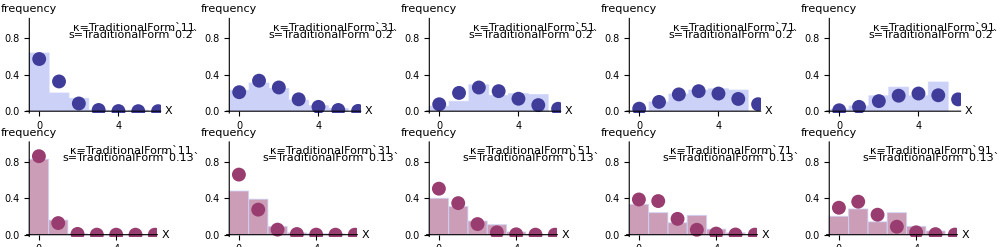

```mathematica
xmax=6;

params={s->0.2,d->0.05,N0->10^4,h->0.5,u->0,m->0,B->2};
Simplify[PDF[BinomialDistribution[k,p],X],{0≤X≤k}];
plot1=
Table[
pdf=%/.p->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.params;
theory=Table[{X,pdf},{X,0,xmax}];
theoryplot=ListPlot[theory,PlotStyle->AbsolutePointSize[10]];
folder=StringForm["nestablish_s``",NumberForm[s/.params,{3,2}]];
data=Import[datadir<>ToString[folder]<>"/data/nestablish_k"<>ToString[k]<>".csv"]//Flatten;
dataplot=Histogram[data,{-0.5,xmax-0.5,1},"Probability"];
Show[dataplot,theoryplot,PlotRange->{0,1},AxesLabel->{"X","frequency"},Epilog->{Text[StringForm["κ=``",k],Scaled@{0.8,0.9}],Text[StringForm["s=``",s/.params],Scaled@{0.8,0.825}]}],
{k,11,91,20}
];

params={s->0.13,d->0.05,N0->10^4,h->0.5,u->0,m->0,B->2};
Simplify[PDF[BinomialDistribution[k,p],X],{0≤X≤k}];
plot2=
Table[
pdf=%/.p->pest/.v->w(3+4B-4w)/4/.w->(1+s/2)(1-d)/.params;
theory=Table[{X,pdf},{X,0,xmax}];
theoryplot=ListPlot[theory,PlotStyle->{AbsolutePointSize[10],defaultcolors[[2]]}];
folder=StringForm["nestablish_s``",NumberForm[s/.params,{3,2}]];
data=Import[datadir<>ToString[folder]<>"/data/nestablish_k"<>ToString[k]<>".csv"]//Flatten;
dataplot=Histogram[data,{-0.5,xmax-0.5,1},"Probability",ChartStyle->Directive[defaultcolors[[2]],Opacity[0.5]]];
Show[dataplot,theoryplot,PlotRange->{0,1},AxesLabel->{"X","frequency"},Epilog->{Text[StringForm["κ=``",k],Scaled@{0.8,0.9}],Text[StringForm["s=``",s/.params],Scaled@{0.8,0.825}]}],
{k,11,91,20}
];

GraphicsGrid[{plot1,plot2},Spacings->0,ImageSize->1000]
```

The probability of rescue is just the probability at least one establishes

```mathematica
PSGV=(1-Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}]/.X->0)
```

1-(1-ρ)^κ

which when κ ρ is small is roughly

```mathematica
Normal[Series[PSGV/.κ->kp/ρ/.ρ->kp /κ/.kp->kp ϵ,{ϵ,0,1}]]/.kp->κ ρ/.ϵ->1
```

κ ρ

Let’s check this with simulations (100 rescues for each dot)

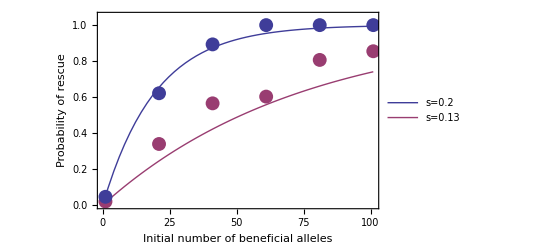

```mathematica
params={s->0.13,d->0.05,N0->10^4,h->0.5,u->0,m->0,B->2};
folder=StringForm["prescue_s``",NumberForm[s/.params,{3,2}]];
Table[
data=Import[datadir<>ToString[folder]<>"/data/prescue_k"<>ToString[κ]<>".csv"]//Flatten;
{κ,Mean[data]//N},
{κ,1,101,20}
];
dataplot=ListPlot[%,PlotStyle->{defaultcolors[[2]],AbsolutePointSize[10]}];

params={s->0.2,d->0.05,N0->10^4,h->0.5,u->0,m->0,B->2};
folder=StringForm["prescue_s``",NumberForm[s/.params,{3,2}]];
Table[
data=Import[datadir<>ToString[folder]<>"/data/prescue_k"<>ToString[κ]<>".csv"]//Flatten;
{κ,Mean[data]//N},
{κ,1,101,20}
];
dataplot2=ListPlot[%,PlotStyle->AbsolutePointSize[10]];

PSGV/.ρ->pest/.v-> w(3+4B-4w)/4/.w->(1+h s)(1-d)/.s->{0.2,0.13}/.params;
theoryplot=Plot[%,{κ,0,101},PlotStyle->Thick,PlotRange->{0,1.05},PlotLegends->Placed[Style[#,labelstyle]&/@{"s=0.2","s=0.13"},Scaled@{0.8,0.2}]];

Show[theoryplot,dataplot,dataplot2,
Frame->{True,True,False,False},
FrameLabel->{"Initial number of beneficial alleles","Probability of rescue"},
LabelStyle->labelstyle,
ImagePadding->padding
]
```

Note this is a bit of an underestimate with smaller selection coefficients. This is likely because smaller selection coefficients allow beneficial alleles to drift at low frequencies for long enough that the wildtype allele becomes rare and homozygote beneficials are made, who have nearly double establishment probabilities.

So the conditioned initial allele frequency is

```mathematica
q0rescueSGV=κ/(2N0)1/PSGV;
```

This is the same in a constant population, just with d=0.

Plot the dynamics

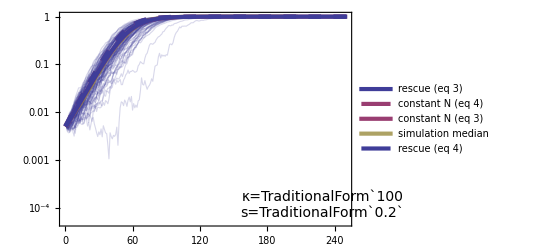

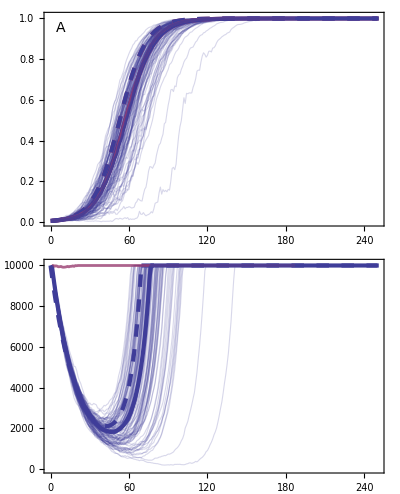

```mathematica
plotDynamicsLog[10^4,0.05,0.2,0.5,100,0,0,100,250]
plotDynamics[10^4,0.05,0.2,0.5,100,0,0,100,250,"A"]
```

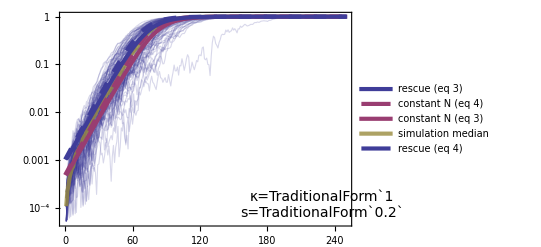

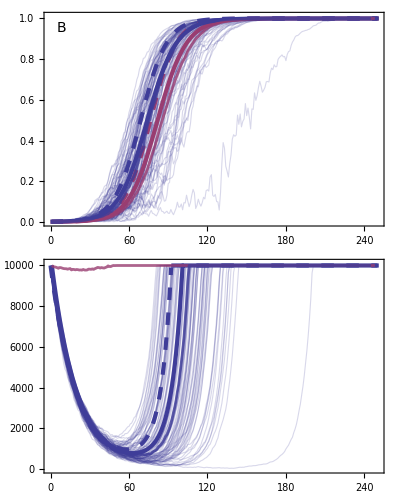

```mathematica
plotDynamicsLog[10^4,0.05,0.2,0.5,1,0,0,100,250]
plotDynamics[10^4,0.05,0.2,0.5,1,0,0,100,250,"B"]
```

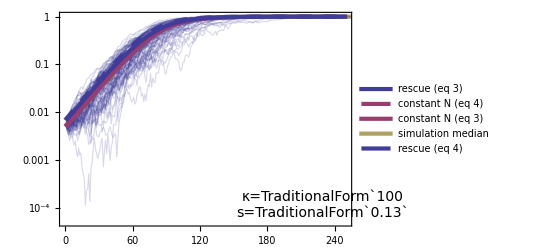

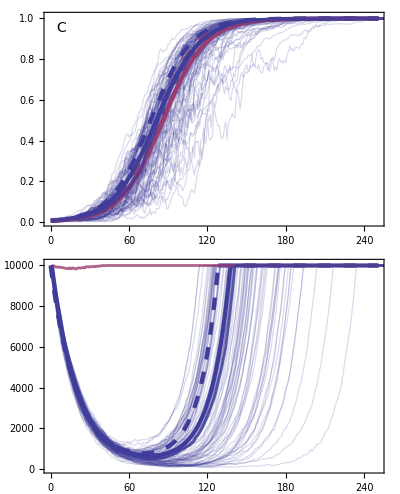

```mathematica
plotDynamicsLog[10^4,0.05,0.13,0.5,100,0,0,100,250]
plotDynamics[10^4,0.05,0.13,0.5,100,0,0,100,250,"C"]
```

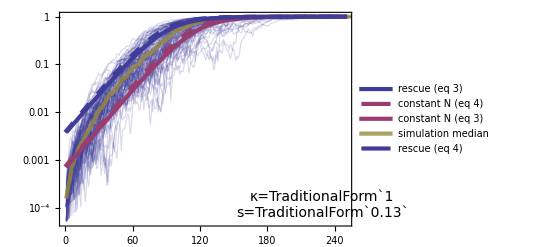

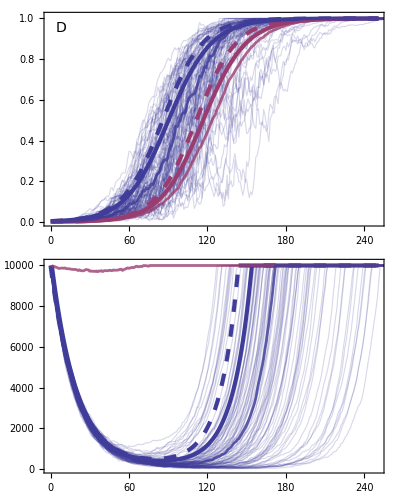

```mathematica
plotDynamicsLog[10^4,0.05,0.13,0.5,1,0,0,100,250]
plotDynamics[10^4,0.05,0.13,0.5,1,0,0,100,250,"D"]
```

The probability that more than one copy of the beneficial allele establishes is the probability of rescue minus the probability that only one establishes

```mathematica
Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}];
PSGV-(%/.X->1)//Simplify
```

1-(1-ρ)^κ-κ (1-ρ)^(-1+κ) ρ

the probability of a soft sweep given rescue is then

```mathematica
Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}];
(PSGV-(%/.X->1))/PSGV//Simplify
%==1-(κ ρ)/(1-ρ)(1-PSGV)/PSGV//Simplify
```

-(-1+(1-ρ)^κ+κ (1-ρ)^(-1+κ) ρ)/(1-(1-ρ)^κ)

True

More specifically, conditioning on at least one copy establishing gives the distribution of the number that establish given rescue

```mathematica
Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}]/PSGV
%/.ρ->pest/.w->(1+s/2)(1-d)/.v->7/4/.s->0.2/.d->0.05/.κ->100;
```

((1-ρ)^(-X+κ) ρ^X Binomial[κ,X])/(1-(1-ρ)^κ)

and from this we can also get the expected number that establish given rescue

```mathematica
Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}]/PSGV;
Simplify[Sum[X %,{X,1,∞}],{0<ρ<1}]
%==(κ ρ)/PSGV
```

(κ ρ)/(1-(1-ρ)^κ)

True

We next plot the probability of a soft sweep given rescue as a function of κ for the two values of s

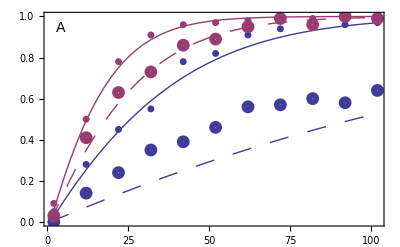

```mathematica
params={s->0.2,d->0.05,N0->10^4,h->0.5,u->0,m->0};

Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}];
(PSGV-(%/.X->1))/PSGV//Simplify;
%/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.B->2/.params;
theory=Plot[%,{κ,1,102},PlotStyle->Thick];

folder=StringForm["softness_rescue_SGV_N``_d``_s``_h``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Length[Select[%%[[i]],#>1&]]/Length[%%[[i]]]},{i,Length[%]}];
data=ListPlot[%,PlotStyle->{defaultcolors[[1]],AbsolutePointSize[5]}];

Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}];
(PSGV-(%/.X->1))/PSGV//Simplify;
%/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)/.B->2/.params;
theoryConstant=Plot[%,{κ,1,102},PlotStyle->{Thick,defaultcolors[[2]]}];

folder=StringForm["softness_rescue_SGV_N``_d0.00_s``_h``",N0/.params,NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Length[Select[%%[[i]],#>1&]]/Length[%%[[i]]]},{i,Length[%]}];
dataConstant=ListPlot[%,PlotStyle->{defaultcolors[[2]],AbsolutePointSize[5]}];

params={s->0.13,d->0.05,N0->10^4,h->0.5,u->0,m->0};

Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}];
(PSGV-(%/.X->1))/PSGV//Simplify;
%/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.B->2/.params;
theory2=Plot[%,{κ,1,102},PlotStyle->{defaultcolors[[1]],Thick,Dashing[Large]}];

folder=StringForm["softness_rescue_SGV_N``_d``_s``_h``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Length[Select[%%[[i]],#>1&]]/Length[%%[[i]]]},{i,Length[%]}];
data2=ListPlot[%,PlotStyle->{defaultcolors[[1]],AbsolutePointSize[5]},PlotMarkers->Graphics[{defaultcolors[[1]],Thickness[0.4],Circle[]},ImageSize->6]];

Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}];
(PSGV-(%/.X->1))/PSGV//Simplify;
%/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)/.B->2/.params;
theoryConstant2=Plot[%,{κ,1,102},PlotStyle->{Thick,defaultcolors[[2]],Dashing[Large]}];

folder=StringForm["softness_rescue_SGV_N``_d0.00_s``_h``",N0/.params,NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Length[Select[%%[[i]],#>1&]]/Length[%%[[i]]]},{i,Length[%]}];
dataConstant2=ListPlot[%,PlotStyle->{defaultcolors[[1]],AbsolutePointSize[5]},PlotMarkers->Graphics[{defaultcolors[[2]],Thickness[0.4],Circle[]},ImageSize->6]];

Show[
theory,data,theoryConstant,dataConstant,theory2,data2,theoryConstant2,dataConstant2,
Frame->{True,True,False,False},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
Epilog->{
Text[Style["A",letterstyle],Scaled@letterposition],
Rotate[Text[Style["Probability of a soft sweep | rescue",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None,
PlotRange->{0,1}
]

Export[imagedir<>"PsoftSGV.pdf",%];
```

and the expected number of copies that establish given rescue

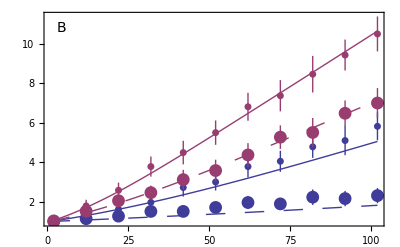

```mathematica
params={s->0.2,d->0.05,N0->10^4,h->0.5,u->0,m->0};

Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}]/PSGV;
Simplify[Sum[X %,{X,1,κ}],{0<ρ<1}];
%/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.B->2/.params;
Table[{κ,%},{κ,1,102}];
theory=ListPlot[%,Joined->True,PlotStyle->Thick];

folder=StringForm["softness_rescue_SGV_N``_d``_s``_h``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Mean[%%[[i]]],StandardDeviation[%%[[i]]]/√Length[%]},{i,Length[%]}];
data=ErrorListPlot[%,PlotStyle->AbsolutePointSize[5]];

Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}]/PSGV;
Simplify[Sum[X %,{X,1,κ}],{0<p<1}];
%/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)/.B->2/.params;
Table[{κ,%},{κ,1,102}];
theoryConstant=ListPlot[%,Joined->True,PlotStyle->Directive[Thick,defaultcolors[[2]]]];

folder=StringForm["softness_rescue_SGV_N``_d0.00_s``_h``",N0/.params,NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Mean[%%[[i]]],StandardDeviation[%%[[i]]]/√Length[%]},{i,Length[%]}];
dataConstant=ErrorListPlot[%,PlotStyle->Directive[defaultcolors[[2]],AbsolutePointSize[5]]];

params={s->0.13,d->0.05,N0->10^4,h->0.5,u->0,m->0};

Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}]/PSGV;
Simplify[Sum[X %,{X,1,κ}],{0<ρ<1}];
%/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)(1-d)/.B->2/.params;
Table[{κ,%},{κ,1,102}];
theory2=ListPlot[%,Joined->True,PlotStyle->{Thick,Dashing[Large]}(*,PlotLegends->Placed[LineLegend[{Directive[defaultcolors[[1]],Thick],Directive[defaultcolors[[2]],Thick]},Style[#,labelstyle]&/@{"s=0.2","s=0.13"}],Scaled@{0.2,0.7}]*)];

folder=StringForm["softness_rescue_SGV_N``_d``_s``_h``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Mean[%%[[i]]],StandardDeviation[%%[[i]]]/√Length[%]},{i,Length[%]}];
data2=ErrorListPlot[%,PlotMarkers->Graphics[{defaultcolors[[1]],Thickness[0.4],Circle[]},ImageSize->6]];

Simplify[PDF[BinomialDistribution[κ,ρ],X],{0≤X≤κ}]/PSGV;
Simplify[Sum[X %,{X,1,κ}],{0<ρ<1}];
%/.ρ->pest/.v->w(3+4B-4w)/4/.w->(1+s h)/.B->2/.params;
Table[{κ,%},{κ,1,102}];
theoryConstant2=ListPlot[%,Joined->True,PlotStyle->{Thick,defaultcolors[[2]],Dashing[Large]}];

folder=StringForm["softness_rescue_SGV_N``_d0.00_s``_h``",N0/.params,NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Mean[%%[[i]]],StandardDeviation[%%[[i]]]/√Length[%]},{i,Length[%]}];
dataConstant2=ErrorListPlot[%,PlotStyle->defaultcolors[[2]],PlotMarkers->Graphics[{defaultcolors[[2]],Thickness[0.4],Circle[]},ImageSize->6]];

Show[
theory,data,theoryConstant,dataConstant,theory2,data2,theoryConstant2,dataConstant2,
Frame->{True,True,False,False},
FrameLabel->{"Initial number of beneficial alleles"},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
PlotRange->All,
Epilog->{
Text[Style["B",letterstyle],Scaled@letterposition],
Rotate[Text[Style["Lineages remaining at rescue",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

Export[imagedir<>"NumberEstSGV.pdf",%];
```

Again, these are underestimates for weaker selection coefficients, when the beneficial allele can drift for long enough that the wildtype is rare and thus homozygotes are made, increasing establishment probabilities.

### Rescue from de novo mutation (equations 8-11, figures 3-4)

The first successful rescue mutation arrives according to a time-inhomogeneous Poisson process with rate λ(t) = 2 N(t) u ρ, so that the probability of at it arriving by time T is 1-exp(-(∫_0)^T λ(t)dt). Therefore the probability of rescue is

```mathematica
Integrate[2N0 Exp[-d t] u ρ,{t,0,T}]//Simplify;
PDNM=Limit[1-Exp[-%],T->∞,Assumptions->d>0]
```

1-ⅇ^(-(2 N0 u ρ)/d)

Taking the derivative of the approximate cumulative distribution function with respect to T and dividing by the probability of rescue gives the PDF of waiting times until the first rescue mutation

```mathematica
1-Exp[-Integrate[λ[t],{t,0,T}]]
D[%,T]/PDNM/.λ[t_]->2N0 Exp[-d t] u ρ/.T->t
```

1-ⅇ^(-∫_0^T λ[t]ⅆt)

(2 ⅇ^(-d t-(2 (1-ⅇ^(-d t)) N0 u ρ)/d) N0 u ρ)/(1-ⅇ^(-(2 N0 u ρ)/d))

Let’s call c the expected number of mutations, then

```mathematica
1-Exp[-Integrate[λ[t],{t,0,T}]];
D[%,T]/PDNM/.λ[t_]->2N0 Exp[-d t] u ρ/.T->t;
%/.u->c/(2N0 ρ/d)
```

(c d ⅇ^(-c (1-ⅇ^(-d t))-d t))/(1-ⅇ^-c)

The first establishing mutation, arriving at time τ, will grow in number nearly exponentially, at rate ρ/2, while it is rare. And given that it establishes will very quickly reach 1/ρ copies. Integrating over the arrival times τ then gives the expected number of copies t generations after environmental change

```mathematica
1-Exp[-Integrate[λ[t],{t,0,T}]];
D[%,T]/PDNM/.λ[t_]->2N0 Exp[-d t] u ρ/.T->t;
%/.u->c/(2N0 ρ/d)/.t->τ;
Integrate[(Exp[ρ/2(t-τ)]/ρ)%,{τ,0,∞},Assumptions->{d>0,ρ>0}]
```

((-c)^(-ρ/(2 d)) ⅇ^((t ρ)/2) (-Gamma[1+ρ/(2 d)]+Gamma[1+ρ/(2 d),-c]))/((-1+ⅇ^c) ρ)

so that it is as if the initial frequency was

```mathematica
1-Exp[-Integrate[λ[t],{t,0,T}]];
D[%,T]/PDNM/.λ[t_]->2N0 Exp[-d t] u ρ/.T->t;
%/.u->c/(2N0 ρ/d)/.t->τ;
Integrate[(Exp[ρ/2(t-τ)]/ρ)%,{τ,0,∞},Assumptions->{d>0,ρ>0}];
1/(2N0)%/ⅇ^((ρ t)/2)//Simplify
q0rescueDNM=%/.c->u 2N0 ρ/d;
```

((-c)^(-ρ/(2 d)) (-Gamma[1+ρ/(2 d)]+Gamma[1+ρ/(2 d),-c]))/(2 (-1+ⅇ^c) N0 ρ)

When the expected number of rescue mutations, c, is very small this reduces to the Orr & Unckless 2014 result

```mathematica
1-Exp[-Integrate[λ[t],{t,0,T}]];
D[%,T]/PDNM/.λ[t_]->2N0 Exp[-d t] u ρ/.T->t;
%/.u->c/(2N0 ρ/d)/.t->τ;
Integrate[(Exp[ρ/2(t-τ)]/ρ)%,{τ,0,∞},Assumptions->{d>0,ρ>0}];
1/(2N0)%/ⅇ^((ρ t)/2)//Simplify;
Simplify[Series[%,{c,0,0}]//Normal,{c>0,ρ>0,d>0}]
```

d/(2 d N0 ρ+N0 ρ^2)

In a population of constant size the waiting time is exponential, so that the waiting time factor is

```mathematica
Simplify[PDF[ExponentialDistribution[λ],τ],τ>0];
Integrate[(Exp[ρ/2(t-τ)])%,{τ,0,∞},Assumptions->{λ>0,ρ>0}];
Simplify[%/ⅇ^((ρ t)/2)/.λ->2N0 u ρ]
```

(4 N0 u)/(1+4 N0 u)

so that it is as if the initial frequency was

```mathematica
Simplify[PDF[ExponentialDistribution[λ],τ],τ>0];
Integrate[(Exp[ρ/2(t-τ)])%,{τ,0,∞},Assumptions->{λ>0,ρ>0}];
Simplify[%/ⅇ^((ρ t)/2)/.λ->2N0 u ρ];
1/(2N0)1/ρ%
q0sweepDNM=%;
```

(2 u)/((1+4 N0 u) ρ)

Plot the dynamics

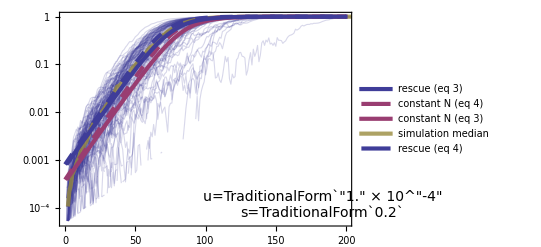

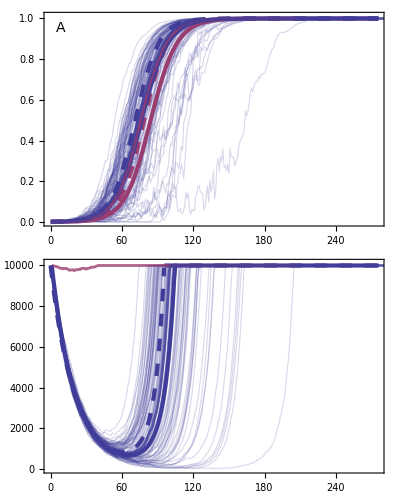

```mathematica
plotDynamicsLog[10^4,0.05,0.2,0.5,0,10.^-4,0,100,200]
plotDynamics[10^4,0.05,0.2,0.5,0,10.^-4,0,100,275,"A"]
```

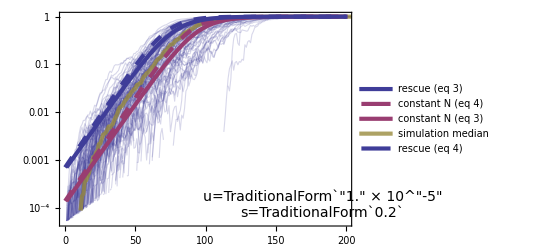

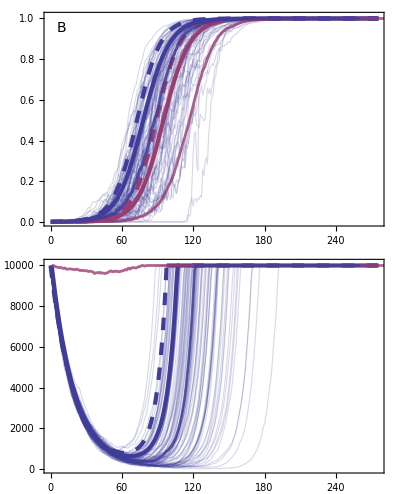

```mathematica
plotDynamicsLog[10^4,0.05,0.2,0.5,0,10.^-5,0,100,200]
plotDynamics[10^4,0.05,0.2,0.5,0,10.^-5,0,100,275,"B"]
```

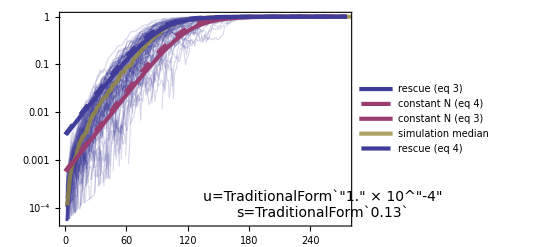

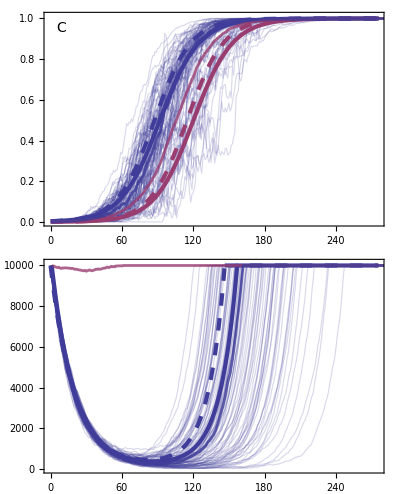

```mathematica
plotDynamicsLog[10^4,0.05,0.13,0.5,0,10.^-4,0,100,275]
plotDynamics[10^4,0.05,0.13,0.5,0,10.^-4,0,100,275,"C"]
```

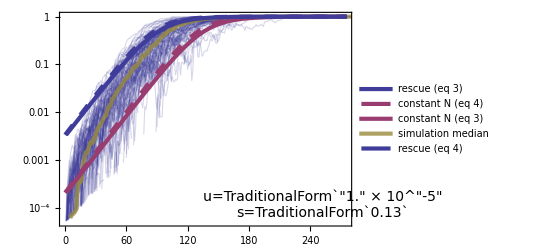

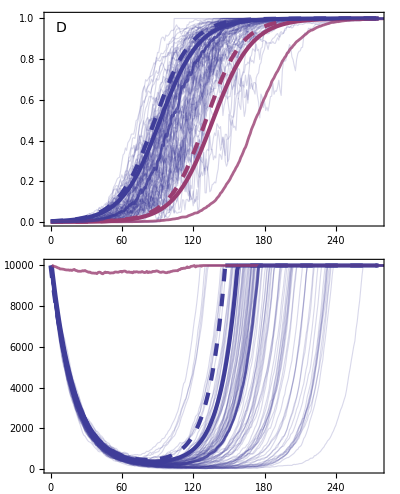

```mathematica
plotDynamicsLog[10^4,0.05,0.13,0.5,0,10.^-5,0,100,275]
plotDynamics[10^4,0.05,0.13,0.5,0,10.^-5,0,100,275,"D"]
```

Establishing A alleles arrive at rate 2N[t](1-q[t])u ρ. For the first successful mutation, the population is overwhelming composed of a alleles and hence q is essentially zero at all previous times and N[t] declines exponentially at rate d. This allows us to derive the relatively simple results above. However, once A has established, the arrival of future successful mutations is complicated by the fact that q is no longer a constant and N[t] is no longer declining as a simple exponential. Now the mutation rate can be increased by an upswing in N, but this is reduced by declining numbers of a alleles.

We can use our recursions above to write the arrival rate, λ[t], in the next generation as a function of the arrival rate in the current generation

```mathematica
2 (wbar n[t])(1-qnew)u ρ//Simplify
%/.u->λ[t]/(2 n[t](1-q[t])ρ)//Simplify
```

2 (-1+d) u ρ n[t] (-1+q[t]) (1+h s q[t])

-(-1+d) (1+h s q[t]) λ[t]

and we see that for h≠0 this also depends on allele frequency because the A alleles prolong the persistence time of the a alleles.

When h≠0 we therefore see a non-exponential decline of a alleles due to selection in heterozygotes

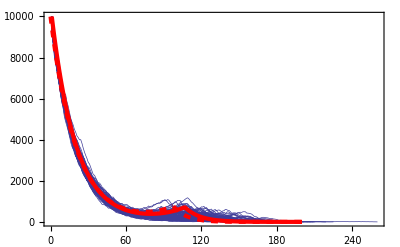

```mathematica
params={s->0.2,h->0.5,N0->10^4,d->0.05,k->0,u->10.^-5,m->0};
maxrep=100;
tmax=200;
legendplace={6.5/8,1/4};

(*rescue: simulations*)
SetDirectory[NotebookDirectory[]];
folder=StringForm["rescue_N``_d``_s``_h``_k``_u``_m``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}],k/.params,NumberForm[u/.params,{6,5}],m/.params];
Clear[data]
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/dynamics_"<>ToString[i-1]<>".txt", "Table", "FieldSeparators"->" "],{i,maxrep}];
na=Table[(1-data[i][[2;;,3]])data[i][[2;;,2]],{i,maxrep}];

(*rescue: theory*)
q0=q0rescueDNM/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2;
numerics=RecurrenceTable[{n[t+1]== Min[n[t] wbar,N0],q[t+1]==qnew,n[0]==N0,q[0]==q0}/.params,{n,q},{t,0,tmax}];
nanumerics=Table[{t,numerics[[t,1]]*(1-numerics[[t,2]])},{t,1,tmax}];
theoryq= q[t]/.qtadditive/.params;
theoryn= Min[Re[n[t]],N0]/.ntadditive/.params;
theoryn2= n[t]/.ntadditive/.params;

Show[
ListPlot[
 na,
Joined->True,
PlotStyle->Directive[AbsoluteThickness[1/2],defaultcolors[[1]]],
PlotRange->All
],
ListPlot[
nanumerics,
Joined->True,
PlotStyle->Directive[AbsoluteThickness[3],Red],
PlotLegends->Placed[LineLegend[Style[#,labelstyle]&/@{"theory (eq 3)"}],Scaled@legendplace],
PlotRange->All
],
Plot[
{(1-theoryq)*theoryn(*,(1-theoryq)*theoryn2*)},{t,0,tmax},
PlotStyle->Directive[AbsoluteThickness[3],Dashed,Red],
PlotLegends->Placed[LineLegend[Style[#,labelstyle]&/@{"theory (eq 4)"}],Scaled@legendplace],
PlotRange->All
],
Frame->{True,True,False,False},
FrameStyle->labelstyle,
FrameLabel->{"Generation"},
PlotRangePadding->None,
ImagePadding->padding,
PlotRangeClipping->False,
Epilog->{
Rotate[Text[Style["Number of a alleles",labelstyle],Scaled@ylabelposition],π/2]
},
PlotRange->{0,N0/.params}
]

Clear[q0]
```

but it ain’t too far off from exponential for these parameters:

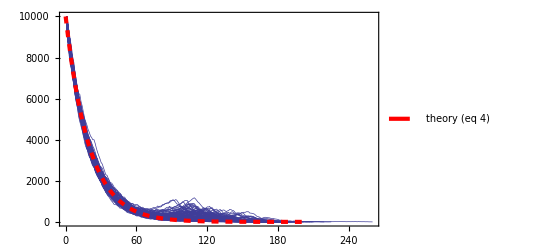

```mathematica
params={s->0.2,h->0.5,N0->10^4,d->0.05,k->0,u->10.^-5,m->0};
maxrep=100;
tmax=200;
legendplace={6.5/8,1/4};

(*rescue: simulations*)
SetDirectory[NotebookDirectory[]];
folder=StringForm["rescue_N``_d``_s``_h``_k``_u``_m``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}],k/.params,NumberForm[u/.params,{6,5}],m/.params];
Clear[data]
Table[data[i]=Import[datadir<>ToString[folder]<>"/data/dynamics_"<>ToString[i-1]<>".txt", "Table", "FieldSeparators"->" "],{i,maxrep}];
na=Table[(1-data[i][[2;;,3]])data[i][[2;;,2]],{i,maxrep}];

(*rescue: theory*)
q0=q0rescueDNM/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2;
theory=N0 Exp[-d t]/.params;

Show[
ListPlot[
 na,
Joined->True,
PlotStyle->Directive[AbsoluteThickness[1/2],defaultcolors[[1]]],
PlotRange->All
],
Plot[
{theory},{t,0,tmax},
PlotStyle->Directive[AbsoluteThickness[3],Dashed,Red],
PlotLegends->Placed[LineLegend[Style[#,labelstyle]&/@{"theory (eq 4)"}],Scaled@legendplace],
PlotRange->All
],
Frame->{True,True,False,False},
FrameStyle->labelstyle,
FrameLabel->{"Generation"},
PlotRangePadding->None,
ImagePadding->padding,
PlotRangeClipping->False,
Epilog->{
Rotate[Text[Style["Number of a alleles",labelstyle],Scaled@ylabelposition],π/2]
},
PlotRange->{0,N0/.params}
]

Clear[q0]
```

So we will use this exponential approximation, which will in general provide an understimate when h>0, and will get worse as h and s and u increase.

We therefore can just use the same rate of arrival of successful mutants that we used for the first mutant and the number of mutations that are expected to establish is

```mathematica
Integrate[2N0 Exp[-d t]ρ u,{t,0,∞},Assumptions->d>0];
Simplify[PDF[PoissonDistribution[%],X],Assumptions->X≥0]
```

(2^X ⅇ^(-(2 N0 u ρ)/d) ((N0 u ρ)/d)^X)/(X!)

giving probability of a soft sweep

```mathematica
Integrate[2N0 Exp[-d t]ρ u,{t,0,∞},Assumptions->d>0];
Simplify[PDF[PoissonDistribution[%],X],Assumptions->X≥0];
PDNM-(%/.X->1)//Simplify
FullSimplify[%==PDNM+(1-PDNM)Log[1-PDNM],{N0>0,u>0,ρ>0,d>0}]
```

1-(ⅇ^(-(2 N0 u ρ)/d) (d+2 N0 u ρ))/d

True

which is essentially the result of Wilson et al 2017 Genetics, who modeled a haploid population, when we ignore density-dependence (just a slight change to the Poisson rate in their equation 7 due to diploidy and our life-cycle).

And the number of mutations that establish once conditioned on rescue is

```mathematica
Integrate[2N0 Exp[-d t]ρ u,{t,0,∞},Assumptions->d>0];
Simplify[PDF[PoissonDistribution[%],X],Assumptions->X≥0];
%/PDNM
```

(2^X ⅇ^(-(2 N0 u ρ)/d) ((N0 u ρ)/d)^X)/((1-ⅇ^(-(2 N0 u ρ)/d)) X!)

so that the probability of a soft sweep given rescue is

```mathematica
Integrate[2N0 Exp[-d t]ρ u,{t,0,∞},Assumptions->d>0];
Simplify[PDF[PoissonDistribution[%],X],Assumptions->X≥0];
%/PDNM;
1-(%/.X->1)//Simplify
FullSimplify[%==1+(1-PDNM)/PDNM Log[1-PDNM],{N0>0,u>0,ρ>0,d>0}]
```

1+(2 N0 u ρ)/(d-d ⅇ^((2 N0 u ρ)/d))

True

Let’s look at the probability of a soft sweep given rescue across a range of mutation rates for these two selection coefficients

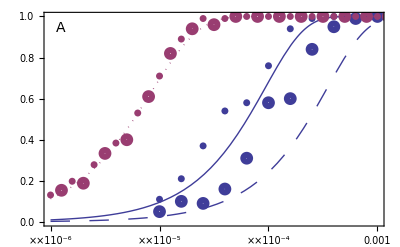

```mathematica
params={s->0.2,d->0.05,N0->10^4,h->0.5};

Integrate[2N0 Exp[-d t]ρ u,{t,0,∞},Assumptions->d>0];
Simplify[PDF[PoissonDistribution[%],X],Assumptions->X≥0];
%/PDNM;
1-(%/.X->1);
%/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.params;
theory=LogLinearPlot[%,{u,10^-6,10^-3},PlotStyle->Thick];

folder=StringForm["softness_rescue_DNM_N``_d``_s``_h``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
where=Position[Length/@%,_?(#≥100&)]//Flatten;
%%[[where,1;;100]];
GatherBy[%%%%,First][[where,1,1]];
Table[{%[[i]],Length[Select[%%[[i]],#>1&]]/Length[%%[[i]]]},{i,Length[%]}];
data=ListLogLinearPlot[%,PlotStyle->{AbsolutePointSize[5]}];

folder=StringForm["softness_rescue_DNM_N``_d0.00_s``_h``",N0/.params,NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Length[Select[%%[[i]],#>1&]]/Length[%%[[i]]]},{i,Length[%]}];
dataConstant=ListLogLinearPlot[%,PlotStyle->{AbsolutePointSize[5],defaultcolors[[2]]}];

params={s->0.13,d->0.05,N0->10^4,h->0.5,N0->10^4,NeN->4/7};

Integrate[2N0 Exp[-d t]ρ u,{t,0,∞},Assumptions->d>0];
Simplify[PDF[PoissonDistribution[%],X],Assumptions->X≥0];
%/PDNM;
1-(%/.X->1);
%/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.params;
theory2=LogLinearPlot[%,{u,10^-6,10^-3},PlotStyle->Directive[Thick,Dashing[Large]]];

folder=StringForm["softness_rescue_DNM_N``_d``_s``_h``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
where=Position[Length/@%,_?(#≥100&)]//Flatten;
%%[[where,1;;100]];
GatherBy[%%%%,First][[where,1,1]];
Table[{%[[i]],Length[Select[%%[[i]],#>1&]]/Length[%%[[i]]]},{i,Length[%]}];
data2=ListLogLinearPlot[%,PlotMarkers->Graphics[{defaultcolors[[1]],Thickness[0.4],Circle[]},ImageSize->6]];

folder=StringForm["softness_rescue_DNM_N``_d0.00_s``_h``",N0/.params,NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Length[Select[%%[[i]],#>1&]]/Length[%%[[i]]]},{i,Length[%]}];
dataConstant2=ListLogLinearPlot[%,PlotMarkers->Graphics[{defaultcolors[[2]],Thickness[0.4],Circle[]},ImageSize->6]];

1-Product[j/(j+θ),{j,n-1}]/.n->2N0/.θ->2N0 NeN u/.params//N;
theoryConstant=LogLinearPlot[%,{u,10^-6,10^-3},PlotStyle->Directive[Thick,defaultcolors[[2]],Dotted]];

Show[
theory,data,theory2,data2,theoryConstant,dataConstant,dataConstant2,
Frame->{True,True,False,False},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
Epilog->{
Text[Style["A",letterstyle],Scaled@letterposition],
Rotate[Text[Style["Probability of a soft sweep | rescue",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

Export[imagedir<>"PsoftDNM.pdf",%];
```

and the expected number of copies of the beneficial allele that establish given rescue

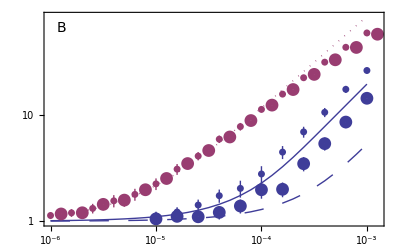

```mathematica
params={s->0.2,d->0.05,N0->10^4,h->0.5};

Integrate[2N0 Exp[-d t]ρ u,{t,0,∞},Assumptions->d>0];
Simplify[PDF[PoissonDistribution[%],X],Assumptions->X≥0];
%/PDNM;
Simplify[Sum[X %,{X,1,∞}],{0<p<1}];
%/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.params;
Table[{10^x,%/.u->10^x},{x,-6,-3,0.1}];
theory=ListLogLogPlot[%,Joined->True,PlotStyle->Thick,PlotRange->{1,1000},Frame->True,FrameTicks->{{Automatic,Automatic},{{{10^-6,"10^-6"},{10^-5,"10^-5"},{10^-4,"10^-4"},{10^-3,"10^-3"}},Automatic}}];

folder=StringForm["softness_rescue_DNM_N``_d``_s``_h``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
where=Position[Length/@%,_?(#≥100&)]//Flatten;
%%[[where,1;;100]];
GatherBy[%%%%,First][[where,1,1]];
Table[{%[[i]],Mean[%%[[i]]],StandardDeviation[%%[[i]]]/√Length[%]},{i,Length[%]}];
ErrorListPlot[%,PlotStyle->{defaultcolors[[1]],AbsolutePointSize[5]}];
data=%/.{x_Real,y_Real}->{Log@x,Log@y};

folder=StringForm["softness_rescue_DNM_N``_d0.00_s``_h``",N0/.params,NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Mean[%%[[i]]],StandardDeviation[%%[[i]]]/√Length[%]},{i,Length[%]}];
ErrorListPlot[%,PlotStyle->{defaultcolors[[2]],AbsolutePointSize[5]}];
dataConstant=%/.{x_Real,y_Real}->{Log@x,Log@y};

params={s->0.13,d->0.05,N0->10^4,h->0.5,NeN->4/7};

Integrate[2N0 Exp[-d t]ρ u,{t,0,∞},Assumptions->d>0];
Simplify[PDF[PoissonDistribution[%],X],Assumptions->X≥0];
%/PDNM;
Simplify[Sum[X %,{X,1,∞}],{0<p<1}];
%/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.params;
Table[{10^x,%/.u->10^x},{x,-6,-3,0.1}];
theory2=ListLogLogPlot[%,Joined->True,PlotStyle->{Thick,Dashing[Large]},PlotRange->{1,All}];

folder=StringForm["softness_rescue_DNM_N``_d``_s``_h``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
where=Position[Length/@%,_?(#≥100&)]//Flatten;
%%[[where,1;;100]];
GatherBy[%%%%,First][[where,1,1]];
Table[{%[[i]],Mean[%%[[i]]],StandardDeviation[%%[[i]]]/√Length[%]},{i,Length[%]}];
ErrorListPlot[%,PlotMarkers->Graphics[{defaultcolors[[1]],Thickness[0.4],Circle[]},ImageSize->6]];
data2=%/.{x_Real,y_Real}->{Log@x,Log@y};

folder=StringForm["softness_rescue_DNM_N``_d0.00_s``_h``",N0/.params,NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Mean[%%[[i]]],StandardDeviation[%%[[i]]]/√Length[%]},{i,Length[%]}];
ErrorListPlot[%,PlotStyle->{defaultcolors[[2]],AbsolutePointSize[5]},PlotMarkers->Graphics[{defaultcolors[[2]],Thickness[0.4],Circle[]},ImageSize->6]];
dataConstant2=%/.{x_Real,y_Real}->{Log@x,Log@y};

Sum[θ/(j-1+θ),{j,n}]/.θ->2N0 NeN u/.n->2*N0/.params;
theoryConstant=LogLogPlot[%,{u,10^-6,10^-3},PlotStyle->{Thick,defaultcolors[[2]],Dotted}];

Show[theory,data,theory2,data2,theoryConstant,dataConstant,dataConstant2,
PlotRange->All,
Frame->{True,True,False,False},
FrameLabel->{"Mutation rate at beneficial locus"},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
Epilog->{
Text[Style["B",letterstyle],Scaled@letterposition],
Rotate[Text[Style["Number of unique copies at rescue",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

Export[imagedir<>"NumberEstDNM.pdf",%];
```

### Rescue from migration (equations S3-S4, figure S6)

If we assume beneficial alleles arrive at constant rate m then the probability a successful one has not arrived by time t is

```mathematica
PDF[PoissonDistribution[m ρ t],X]/.X->0
```

ⅇ^(-m t ρ)

The population is expected to go extinct in

```mathematica
Solve[1==N0 Exp[-d t],t]/.C[1]->0//Flatten
```

{t→Log[N0]/d}

generations and thus the probability of rescue by a migrant allele is roughly the probability at least one has established by then

```mathematica
Solve[1==N0 Exp[-d t],t]/.C[1]->0//Flatten;
PMIG=1-PDF[PoissonDistribution[m ρ t],X]/.X->0/.%
```

1-N0^(-(m ρ)/d)

The PDF of waiting times until the first successful migrant allele arrives, given one arrives, is a truncated exponential

```mathematica
1-PDF[PoissonDistribution[m ρ t],X]/.X->0;
Ft=D[%,t]/PMIG
Simplify[%==PDF[ExponentialDistribution[m ρ],t]/PMIG,t>0]
Integrate[%%,{t,0,Log[N0]/d}]==1
```

(ⅇ^(-m t ρ) m ρ)/(1-N0^(-(m ρ)/d))

True

True

which becomes more uniform as m (and therefore the probability of rescue) decreases

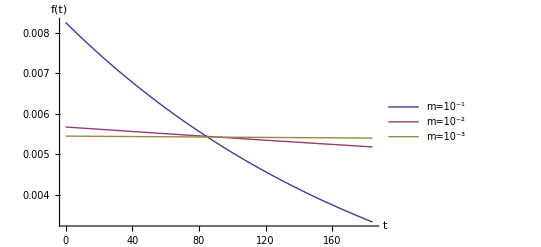

```mathematica
Ft/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.d->0.05/.s->0.2/.h->0.5/.N0->10^4/.m->{10^-1,10^-2,10^-3};
Plot[%,{t,0,Log[N0]/d/.N0->10^4/.d->0.05},PlotRange->{0,All},AxesLabel->{"t","f(t)"},PlotLegends->{"m=10^-1","m=10^-2","m=10^-3"}]
```

So the expected number of copies of the beneficial allele at time t, while rare, is

```mathematica
Solve[1==N0 Exp[-d t],t]/.C[1]->0//Flatten;
Integrate[Exp[ρ (t-τ)/2]/ρ(Ft/.t->τ),{τ,0,t/.%}]
```

(2 (ⅇ^((t ρ)/2)-ⅇ^(1/2 ρ (t-((1+2 m) Log[N0])/d))) m)/((1-N0^(-(m ρ)/d)) (ρ+2 m ρ))

so that it is as if the initial frequency was

```mathematica
Solve[1==N0 Exp[-d t],t]/.C[1]->0//Flatten;
Integrate[Exp[ρ(t- τ)/2]/ρ(Ft/.t->τ),{τ,0,t/.%}];
Simplify[1/(2N0)%/Exp[ρ t/2]];
%==1/(2N0)1/ρ(2m  (1-N0^(-ρ/(2 d)-(m ρ)/d)))/((1+2 m) (1-N0^((-m ρ)/d)))//Simplify
q0rescueMIG=1/(2N0)1/ρ(2m  (1-N0^(-ρ/(2 d)-(m ρ)/d)))/((1+2 m) (1-N0^((-m ρ)/d)));
```

True

When (m ρ)/d is small this is nearly independent of m (as in the case of rescue by DNM)

```mathematica
Series[1/(2N0)1/ρ(2m  (1-N0^(-ρ/(2 d)-(m ρ)/d)))/((1+2 m) (1-N0^((-m ρ)/d)))/.m->mpoverd d/ρ,{mpoverd,0,0}]//Normal//Simplify
```

(d (1-N0^(-ρ/(2 d))))/(N0 ρ^2 Log[N0])

In a population of constant size the waiting time is a simple exponential so that waiting time factor is

```mathematica
Simplify[PDF[ExponentialDistribution[m ρ],τ],τ≥0];
Simplify[Integrate[Exp[ρ (t-τ)/2]%,{τ,0,∞}],{m>0,ρ>0}];
%/Exp[ρ t/2]
```

(2 m)/(1+2 m)

so it is as if the initial frequency was

```mathematica
Simplify[PDF[ExponentialDistribution[m ρ],τ],τ≥0];
Simplify[Integrate[Exp[ρ (t-τ)/2]%,{τ,0,∞}],{m>0,ρ>0}];
%/Exp[ρ t/2];
1/(2N0)1/ρ%
q0sweepMIG=%;
```

m/((1+2 m) N0 ρ)

Plot some dynamics

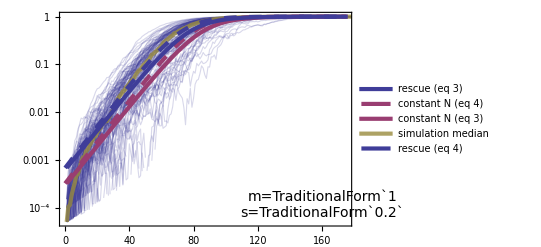

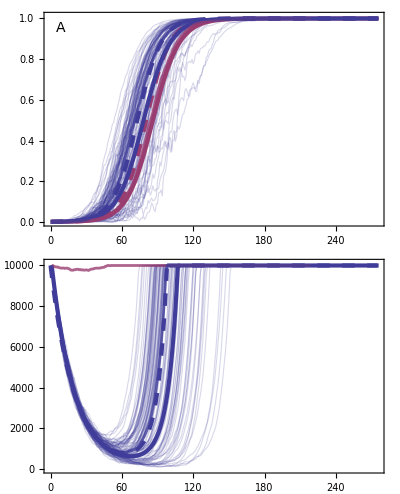

```mathematica
plotDynamicsLog[10^4,0.05,0.2,0.5,0,0,1,100,175]
plotDynamics[10^4,0.05,0.2,0.5,0,0,1,100,275,"A"]
```

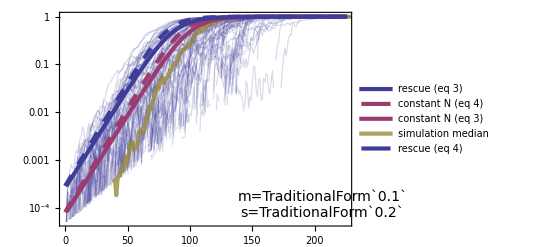

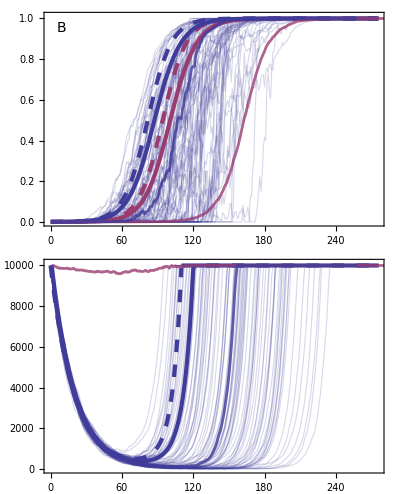

```mathematica
plotDynamicsLog[10^4,0.05,0.2,0.5,0,0,10.^-1,100,225]
plotDynamics[10^4,0.05,0.2,0.5,0,0,10.^-1,100,275,"B"]
```

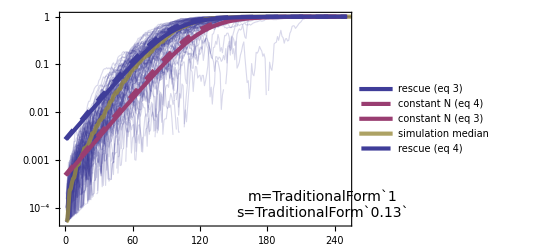

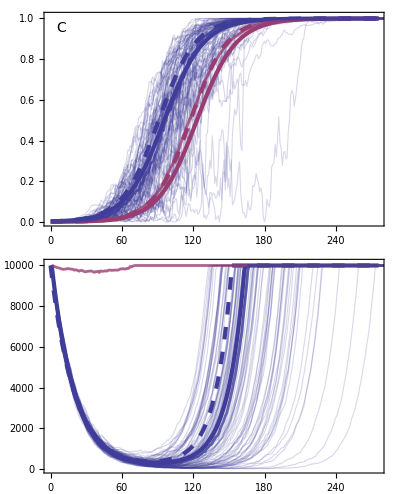

```mathematica
plotDynamicsLog[10^4,0.05,0.13,0.5,0,0,1,100,250]
plotDynamics[10^4,0.05,0.13,0.5,0,0,1,100,275,"C"]
```

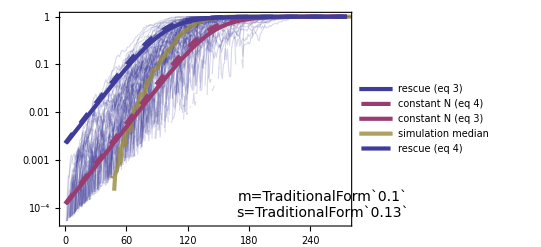

-Graphics-

```mathematica
plotDynamicsLog[10^4,0.05,0.13,0.5,0,0,10.^-1,100,275]
plotDynamics[10^4,0.05,0.13,0.5,0,0,10.^-1,100,275,"D"]
```

## The structured coalescent

### Deriving rates of coalescence, recombination, mutation, and migration

#### Setup

We have a lifecycle that has 
1. census
2. selection
3. recombination
4. syngamy
5. mutation
7. migration
(see Figure S1).

We will be using backwards in time notation here (consistent with Pennings and Hermisson 2006 MBE; hereafter PH2). Given beneficial allele frequency x[τ] and population size n[τ] in generation τ (in the main text we use p’(τ) and N’(τ)) we will give recursions for the frequency of a beneficial allele in the next generation, x[τ-1]. We denote the time of the artificial generation between selection and recombination as τ-1/5, between recombination and syngamy as τ-2/5, between syngamy and mutation as τ-3/5, and between mutation and migration as τ-4/5.

#### Migration

The number of migrant alleles that arrive each generation is Poisson with mean m. Migrant alleles that arrive replace alleles already in the population. If the population size is n, the probability an allele is replaced by a migrant is therefore

```mathematica
Expectation[M/n,M\[Distributed]PoissonDistribution[m]]
```

m/n

The number of beneficial alleles immediately after migration is (which, ignoring carrying capacity is the number in the next generation)

```mathematica
2n[τ-1]x[τ-1]==2n[τ-4/5]x[τ-4/5](1-m/(2n[τ-4/5]))+2n[τ-4/5]x[τ-4/5](m/(2n[τ-4/5]))+ 2n[τ-4/5](1-x[τ-4/5])(m/(2n[τ-4/5]));
```

where the first term is the previous migrants that have not been replaced, the second term is the migrants that have been replaced, and the third term is the non-migrants that have been replaced.

The probability a beneficial allele is a new migrant is therefore

```mathematica
(2n[τ-4/5]x[τ-4/5](m/(2n[τ-4/5]))+ 2n[τ-4/5](1-x[τ-4/5])(m/(2n[τ-4/5])))/(2n[τ-1]x[τ-1])//Simplify
```

m/(2 n[-1+τ] x[-1+τ])

and assuming population size and allele frequency don’t change much from generation to generation we have

```mathematica
Pmig1==m/(2 n[-1+τ] x[-1+τ])/.n[-1+τ] ->n[τ]/.x[-1+τ]->x[τ]
```

Pmig1==m/(2 n[τ] x[τ])

which is a diploid version of equation 15 in PH2, where they’re m is our m/n[τ] (they use m as the probability of being replaced).

The probability at least one of k beneficial alleles is a new migrant is then

```mathematica
1-(1-Pmig1)^k/.Pmig1->m/(2 n[τ] x[τ])
Series[%,{m,0,1}]
```

1-(1-m/(2 n[τ] x[τ]))^k

(k m)/(2 n[τ] x[τ])+O[m]^2

which gives equation 16 in PH2 (again with their m being replaced by m/n[τ]).

#### Mutation

The number of beneficial alleles after mutation is the number before mutation plus the number of new mutants

```mathematica
2n[τ-4/5]x[τ-4/5]==2n[τ-3/5]x[τ-3/5]+u 2n[τ-3/5](1-x[τ-3/5]);
```

so that the frequency of beneficial alleles after mutation is

```mathematica
x[τ-4/5]==n[τ-3/5]/n[τ-4/5] x[τ-3/5]+u n[τ-3/5]/n[τ-4/5](1-x[τ-3/5]);
```

Since the population size does not change during mutation, this simplifies to

```mathematica
x[τ-4/5]==x[τ-3/5]+u (1-x[τ-3/5]);
```

which is analagous to equation 2 in PH2.

The probability a beneficial allele is a new mutant (or the probability a neutral allele was on the ancestral background previously) is therefore

```mathematica
Pmut1==(u (1-x[τ-3/5]))/x[τ-4/5];
```

which, using the previous equation, is

```mathematica
Solve[x[τ-4/5]==x[τ-3/5]+u (1-x[τ-3/5]),x[τ-3/5]]//Flatten;
Pmut1==(u (1-x[τ-3/5]))/x[τ-4/5]/.%//Simplify
```

Pmut1==(u (-1+x[-4/5+τ]))/((-1+u) x[-4/5+τ])

which is analagous to equation 3 in PH2.

The probability that at least one of k beneficial alleles is a new mutant is

```mathematica
Pmut1->(u (-1+x[-4/5+τ]))/((-1+u) x[-4/5+τ]);
1-(1-Pmut1)^k/.%//Simplify
```

1-((u-x[-4/5+τ])/((-1+u) x[-4/5+τ]))^k

When mutation is rare this is approximately

```mathematica
Pmut1->(u (-1+x[-4/5+τ]))/((-1+u) x[-4/5+τ]);
1-(1-Pmut1)^k/.%//Simplify
Normal@Series[%,{u,0,1}]
%==(k u (1-x[τ-4/5]))/x[τ-4/5]//Simplify
```

1-((u-x[-4/5+τ])/((-1+u) x[-4/5+τ]))^k

u (-k+k/x[-4/5+τ])

True

Assuming little change in allele frequency from one generation to the next gives Pmutk in equation 9 of PH2,

```mathematica
(k u (1-x[τ-4/5]))/x[τ-4/5]/.x[τ-4/5]->x[τ]
```

(k u (1-x[τ]))/x[τ]

Note that while PH2 assume haploidy, with diploidy we both double the mutation rate as well as the number of alleles, which cancel.

#### Coalescence

Given that none of the k beneficial alleles migrates or mutates the probability any two (and the neutral alleles on that background) coalesce is (k(k-1)/2)/(2ne[τ-2/5]x[τ-2/5]), where ne is the effective population size. Thus the probability of coalescence is

```mathematica
Binomial[k,2]/(2ne[τ-2/5]x[τ-2/5]);
```

Assuming the effective population size and allele frequency change little from one generation to the next gives the diploid version of PcoalK given in equation 9 of PH2

```mathematica
Binomial[k,2]/(2ne[τ-2/5]x[τ-2/5])/.ne[τ-2/5]->ne[τ]/.x[τ-2/5]->x[τ]
```

((-1+k) k)/(4 ne[τ] x[τ])

#### Recombination

Consider a neutral locus recombination distance r from the selected site. Assuming weak selection such the survivors of viability selection are approximately in Hardy-Weinberg proportions, the number of alleles linked to the selected allele after recombination is

```mathematica
2n[τ-2/5]x[τ-2/5]==2n[τ-1/5]x[τ-1/5](x[τ-1/5]+(1-x[τ-1/5])(1-r))+2n[τ-1/5](1-x[τ-1/5])x[τ-1/5]r==2n[τ-1/5]x[τ-1/5];
```

where the first term on the RHS is the number currently linked to the selected allele multiplied by the probability of being in a homozygote plus the probability of being in a heterozygote and not recombining, and the second term on the RHS is the number not currently linked to the selected allele times the probability of being in a heterozygote and recombining.

Thus, the probability an allele on the selected background among the after recombination was not on that background before recombination is

```mathematica
Prec1==(2n[τ-1/5](1-x[τ-1/5])x[τ-1/5]r)/(2n[τ-2/5]x[τ-2/5]);
```

and since recombination doesn’t change allele frequencies of population size this is

```mathematica
Prec1==(2n[τ-1/5](1-x[τ-1/5])x[τ-1/5]r)/(2n[τ-2/5]x[τ-2/5])/.n[τ-2/5]->n[τ-1/5]/.x[τ-2/5]->x[τ-1/5]
```

Prec1==r (1-x[-1/5+τ])

Therefore the probability at least one of k alleles on the selected background recombine off is

```mathematica
Prec1->r (1-x[-1/5+τ]);
1-(1-Prec1)^k/.%//Simplify
```

1-(1-r+r x[-1/5+τ])^k

Assuming recombination is rare gives

```mathematica
Prec1->r (1-x[-1/5+τ]);
1-(1-Prec1)^k/.%//Simplify;
Normal@Series[%,{r,0,1}]
%==r k (1- x[-1/5+τ])//Simplify
```

r (k-k x[-1/5+τ])

True

And assuming selection changes allele frequency slowly

```mathematica
Preck==r k (1- x[-1/5+τ])/.x[-1/5+τ]->x[τ]
```

Preck==k r (1-x[τ])

which is analagous to the results found in Table 1 of Hudson & Kaplan 1988 (they consider 2 neutral loci so it’s a bit more complicated).

### Coalesence, recombination, mutation, and migration rates (equation 12)

A sample coalesces, recombines or mutates off the selected background, or migrates out of the population with probabilities that depend on the frequency of the beneficial background, x, the total number of chromosomes, 2n, and the number of lineages remaining, k,

```mathematica
pcoal[k_,τ_]:=Binomial[k,2] 1/(2ne[τ]x[τ])
preco[k_,τ_]:=k(2n[τ]r(1-x[τ]))/(2n[τ])
pmut[k_,τ_]:=k (2n[τ]u(1-x[τ]))/(2n[τ]x[τ])
pmig[k_,τ_]:=k m/(2n[τ]x[τ])
```

with τ the number of generations before fixation (in the main text we replace n with N’, ne with N_e', and x with p’).

### The number of successful migrants (equations 14-15, figure 5)

Note that, if ne/n is constant, so is the ratio of migration to coalescence

```mathematica
pmig[k,τ]/(pcoal[k,τ]/.n[τ]->ne[τ])/.ne[τ]->NeN n[τ]
```

(2 m NeN)/(-1+k)

We can therefore use Ewen’s sampling formula to get the distribution of migrant haplotypes among a sample, replacing θ with

```mathematica
Solve[(2 ne[τ] x[τ] pmut[k,τ]/.u->θ/(4ne[τ])/.x[τ]->0)==(2 ne[τ] x[τ]pmig[k,τ]/.n[τ]->ne[τ]/NeN),θ]//Flatten
```

{θ→2 m NeN}

For example, the expected number of migrant haplotypes found in a sample of size n is (Ewens 2004 p 336)

```mathematica
Sum[θ/(j-1+θ),{j,n}]
```

-θ PolyGamma[0,θ]+θ PolyGamma[0,n+θ]

Try that out with simulation data

```mathematica
params={s->0.2,d->0.05,N0->10^4,h->0.5};
m ρ tfixadditive 1/PMIG/.q0->q0rescueMIG;
%/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.params;
theory=LogLogPlot[%,{m,10^-2,10^-0},PlotStyle->Thick];

folder=StringForm["softness_rescue_MIG_N``_d``_s``_h``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Mean[%%[[i]]],StandardDeviation[%%[[i]]]/√Length[%]},{i,Length[%]}];
ErrorListPlot[%,PlotStyle->{defaultcolors[[1]],AbsolutePointSize[5]}];
data=%/.{x_Real,y_Real}->{Log@x,Log@y};

folder=StringForm["softness_rescue_MIG_N``_d0.00_s``_h``",N0/.params,NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Mean[%%[[i]]],StandardDeviation[%%[[i]]]/√Length[%]},{i,Length[%]}];
ErrorListPlot[%,PlotStyle->{defaultcolors[[2]],AbsolutePointSize[5]}];
dataConstant=%/.{x_Real,y_Real}->{Log@x,Log@y};

params={s->0.13,d->0.05,N0->10^4,h->0.5};
m ρ T 1/PMIG/.T->tfixadditive/.q0->q0rescueMIG;
%/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.params;
theory2=LogLogPlot[%,{m,10^-2,1},PlotStyle->{Thick,defaultcolors[[2]]}(*,PlotLegends->Placed[LineLegend[{Directive[defaultcolors[[1]],Thick],Directive[defaultcolors[[2]],Thick]},Style[#,labelstyle]&/@{"s=0.2","s=0.13"}],Scaled@{0.2,0.7}]*)];

folder=StringForm["softness_rescue_MIG_N``_d``_s``_h``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Mean[%%[[i]]],StandardDeviation[%%[[i]]]/√Length[%]},{i,Length[%]}];
ErrorListPlot[%,PlotStyle->defaultcolors[[1]],PlotMarkers->Graphics[{defaultcolors[[1]],Thickness[0.4],Circle[]},ImageSize->6]];
data2=%/.{x_Real,y_Real}->{Log@x,Log@y};

folder=StringForm["softness_rescue_MIG_N``_d0.00_s``_h``",N0/.params,NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Mean[%%[[i]]],StandardDeviation[%%[[i]]]/√Length[%]},{i,Length[%]}];
ErrorListPlot[%,PlotStyle->defaultcolors[[2]],PlotMarkers->Graphics[{defaultcolors[[2]],Thickness[0.4],Circle[]},ImageSize->6]];
dataConstant2=%/.{x_Real,y_Real}->{Log@x,Log@y};

Sum[θ/(j-1+θ),{j,n}]/.θ->2m NeN/.n->2*10^4/.NeN->4/7;
theory3=LogLogPlot[%,{m,10^-2,1},PlotStyle->{Thick,defaultcolors[[3]]}];

Show[(*theory,theory2,*)theory3,data,data2,dataConstant,dataConstant2,
PlotRange->Log@{1,15},
Frame->{True,True,False,False},
FrameLabel->{"Migration rate"},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
Epilog->{
Text[Style["B",letterstyle],Scaled@letterposition],
Rotate[Text[Style["Number of unique copies at rescue",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

Export[imagedir<>"NumberEstMIG.pdf",%];
```

-Graphics-

And the probability of a soft sweep is

```mathematica
Product[j/(j+θ),{j,n-1}]
```

((-1+n)!)/Pochhammer[1+θ,-1+n]

and try that with simulation data

```mathematica
params={s->0.2,d->0.05,N0->10^4,h->0.5};
(PMIG-ⅇ^(-m ρ T) m ρ T)/PMIG/.T->tfixadditive/.q0->q0rescueMIG/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.params;
theory=LogLinearPlot[%,{m,10^-2,10^-0},PlotStyle->Thick];

folder=StringForm["softness_rescue_MIG_N``_d``_s``_h``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Length[Select[%%[[i]],#>1&]]/Length[%%[[i]]]},{i,Length[%]}];
data=ListLogLinearPlot[%,PlotStyle->{defaultcolors[[1]],AbsolutePointSize[5]}];

folder=StringForm["softness_rescue_MIG_N``_d0.00_s``_h``",N0/.params,NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Length[Select[%%[[i]],#>1&]]/Length[%%[[i]]]},{i,Length[%]}];
dataConstant=ListLogLinearPlot[%,PlotStyle->{defaultcolors[[2]],AbsolutePointSize[5]}];

params={s->0.13,d->0.05,N0->10^4,h->0.5};
(PMIG-ⅇ^(-m ρ T) m ρ T)/PMIG/.T->tfixadditive/.q0->q0rescueMIG/.ρ->pest/.v->1/4 (3+4 B-4 w) w/.w->(1+s h)(1-d)/.B->2/.params;
theory2=LogLinearPlot[{,%},{m,10^-2,10^-0},PlotStyle->Thick];

folder=StringForm["softness_rescue_MIG_N``_d``_s``_h``",N0/.params,NumberForm[d/.params,{3,2}],NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Length[Select[%%[[i]],#>1&]]/Length[%%[[i]]]},{i,Length[%]}];
data2=ListLogLinearPlot[%,PlotStyle->defaultcolors[[1]],PlotMarkers->Graphics[{defaultcolors[[1]],Thickness[0.4],Circle[]},ImageSize->6]];

folder=StringForm["softness_rescue_MIG_N``_d0.00_s``_h``",N0/.params,NumberForm[s/.params,{3,2}],NumberForm[h/.params,{2,1}]];
Import[datadir<>ToString[folder]<>"/data/nalleles.csv", "CSV"]//Flatten;
ArrayReshape[%,{Length[%]/2,2}];
GatherBy[%,First][[All,All,2]];
GatherBy[%%,First][[All,1,1]];
Table[{%[[i]],Length[Select[%%[[i]],#>1&]]/Length[%%[[i]]]},{i,Length[%]}];
dataConstant2=ListLogLinearPlot[%,PlotStyle->defaultcolors[[1]],PlotMarkers->Graphics[{defaultcolors[[2]],Thickness[0.4],Circle[]},ImageSize->6]];

1-Product[j/(j+θ),{j,n-1}]/.θ->2m NeN/.n->2*10^4/.NeN->4/7;
theory3=LogLinearPlot[%,{m,10^-2,10^-0},PlotStyle->{defaultcolors[[3]],Thick}];

Show[(*theory,theory2,*)theory3,data,data2,dataConstant,dataConstant2,
Frame->{True,True,False,False},
FrameTicksStyle->{FontColor->White,Automatic,Automatic,Automatic},
LabelStyle->labelstyle,
ImagePadding->{{50,15},{40,10}},
Epilog->{
Text[Style["A",letterstyle],Scaled@letterposition],
Rotate[Text[Style["Probability of a soft sweep | rescue",labelstyle],Scaled@{-0.125,0.5}],π/2]
},
PlotRangeClipping->False,
PlotRangePadding->None
]

Export[imagedir<>"PsoftMIG.pdf",%];
```

-Graphics-

### Approximate backward-time dynamics

If we consider a mutation fixed when it reaches a frequency of 1-1/(2N0) then the fixation time is roughly

```mathematica
1-1/(2N0)==q[t]/.qtadditive;
tfixadditive=t/.Simplify[Solve[%,t]/.C[1]->0//Flatten]
```

(2 Log[-((-1+2 N0) (-1+q0))/q0])/s

and the allele frequency back in time is

```mathematica
q[t]/.qtadditive/.t->tfixadditive-τ//Simplify
qtadditiveback[τ_]:=(-1+2N0)/(-1+ⅇ^((s τ)/2)+2N0)
qtadditiveback[τ]==%%//Simplify
```

(-1+2 N0)/(-1+ⅇ^((s τ)/2)+2 N0)

True

Which is the same as a classic sweep (ie is independent of demography), the only difference being the fixation times.

We can also compute the population size back in time

```mathematica
n[t]/.ntadditive/.t->tfixadditive-τ//Simplify
ntadditiveback[τ_]:=ⅇ^(d (τ-(2 Log[-((-1+2N0) (-1+q0))/q0])/s)) N0 (-ⅇ^(-(s τ)/2) (-1+ⅇ^((s τ)/2)+2N0) (-1+q0))^(2-2 d)
ntadditiveback[τ]==%%//Simplify
```

ⅇ^(d (τ-(2 Log[-((-1+2 N0) (-1+q0))/q0])/s)) N0 (-ⅇ^(-(s τ)/2) (-1+ⅇ^((s τ)/2)+2 N0) (-1+q0))^(2-2 d)

True

### Probability of no events until time τ (integrals of equation 16, which are used for equations 17-18)

The probability of no coalescence in τ generations

```mathematica
cbackapprox[k_,τ_]:=1/(4 N0 (q0-2 N0 q0)^2 NeN)(-1+k) k (-1+2 N0) (-((-1+2 N0) (-1+q0))/q0)^(-2+(2 d)/s) ((N0 (N0/(-1+2 N0))^(-1-2 d) (N0-N0 q0)^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,1/(1-2 N0)])/(d-s+d s)-1/(d-s+d s)ⅇ^((-d+s) τ) (-1+2 N0) ((-1+ⅇ^((s τ)/2)+2 N0)/(-1+2 N0))^(-2 d) (-ⅇ^(-(s τ)/2) (-1+ⅇ^((s τ)/2)+2 N0) (-1+q0))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,ⅇ^((s τ)/2)/(1-2 N0)]+1/(-3 s+2 d (1+s))2 ((N0/(-1+2 N0))^(-2 d) (N0-N0 q0)^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,1/(1-2 N0)]-ⅇ^(-d τ+(3 s τ)/2) ((-1+ⅇ^((s τ)/2)+2 N0)/(-1+2 N0))^(-2 d) (-ⅇ^(-(s τ)/2) (-1+ⅇ^((s τ)/2)+2 N0) (-1+q0))^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,ⅇ^((s τ)/2)/(1-2 N0)]))
(*pcoal[k,t]/.x[t]->qtadditiveback[t]/.ne[t]->ntadditiveback[t]NeN;*)
(*Integrate[%,{t,0,τ},Assumptions->{τ>0}]*)(*slow*)
(*cbackapprox[k,τ]==%//Simplify*)
```

The probability of no recombination in τ generations

```mathematica
rbackapprox[k_,τ_]:=(2k r (Log[1-ⅇ^((s τ)/2)-2 N0]-Log[-2 N0]))/s
(*preco[k,t]/.x[t]->qtadditiveback[t];
Integrate[%,{t,0,τ}];
rbackapprox[k,τ]==%//Simplify*)
```

The probability of no mutation in τ generations

```mathematica
mutbackapprox[k_,τ_]:=(2 (-1+ⅇ^((s τ)/2)) k u)/((-1+2 N0) s)
(*pmut[k,t]/.x[t]->qtadditiveback[t];
Integrate[%,{t,0,τ},Assumptions->{τ>0}];
mutbackapprox[k,τ]==%//Simplify*)
```

The probability of no migration in τ generations

```mathematica
migbackapprox[k_,τ_]:=1/(2 N0 (q0-2 N0 q0)^2 NeN)k m (-1+2 N0) (-((-1+2 N0) (-1+q0))/q0)^(-2+(2 d)/s) ((N0 (N0/(-1+2 N0))^(-1-2 d) (N0-N0 q0)^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,1/(1-2 N0)])/(d-s+d s)-1/(d-s+d s)ⅇ^((-d+s) τ) (-1+2 N0) ((-1+ⅇ^((s τ)/2)+2 N0)/(-1+2 N0))^(-2 d) (-ⅇ^(-(s τ)/2) (-1+ⅇ^((s τ)/2)+2 N0) (-1+q0))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,ⅇ^((s τ)/2)/(1-2 N0)]+1/(-3 s+2 d (1+s))2 ((N0/(-1+2 N0))^(-2 d) (N0-N0 q0)^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,1/(1-2 N0)]-ⅇ^(-d τ+(3 s τ)/2) ((-1+ⅇ^((s τ)/2)+2 N0)/(-1+2 N0))^(-2 d) (-ⅇ^(-(s τ)/2) (-1+ⅇ^((s τ)/2)+2 N0) (-1+q0))^(2 d) Hypergeometric2F1[2-2 d,3-(2 d (1+s))/s,4-(2 d (1+s))/s,ⅇ^((s τ)/2)/(1-2 N0)]))
(*pmig[k,t]/.x[t]->qtadditiveback[t]/.n[t]->ntadditiveback[t]NeN;
Integrate[%,{t,0,τ},Assumptions->{τ>0}](*slow*)*)
(*migbackapprox[k,τ]==%//Simplify*)
```

A population of constant size will have the same recombination and mutation terms (because these depend only on the allele frequency dynamics backwards in time, which are approximately the same, just with different q0), but different coalescence and migration terms

```mathematica
cclassicbackapprox[k_,τ_]:=((-1+k) k ((2 (-1+ⅇ^((s τ)/2)))/s+(-1+2 N0) τ))/(4 N0 (-1+2 N0)NeNc)
pcoal[k,t]/.x[t]->qtadditiveback[t]/.ne[t]->N0 NeNc;
Integrate[%,{t,0,τ},Assumptions->{τ>0}];
cclassicbackapprox[k,τ]==%//Simplify
```

True

```mathematica
migclassicbackapprox[k_,τ_]:=(k m (-2+2 ⅇ^((s τ)/2)+(-1+2 N0) s τ))/(2 N0 (-1+2 N0) s NeNc)
pmig[k,t]/.x[t]->qtadditiveback[t]/.n[t]->N0 NeNc;
Integrate[%,{t,0,τ},Assumptions->{τ>0}];
migclassicbackapprox[k,τ]==%//Simplify
```

True

It is also useful to calculate the probability of coalescence by time T during the population bottleneck (ignoring the sweep)

```mathematica
cbottlebackapprox[k_,τ_]:=1/(4 (1-2 N0)^2 N0 (-1+q0)^2 (d-s+d s) NeN)(-1+k) k (-((-1+2 N0) (-1+q0))/q0)^((2 d)/s) ((N0/(-1+2 N0))^(-2 d) (N0-N0 q0)^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,1/(1-2 N0)]-ⅇ^((-d+s) τ) ((-1+ⅇ^((s τ)/2)+2 N0)/(-1+2 N0))^(-2 d) (-ⅇ^(-(s τ)/2) (-1+ⅇ^((s τ)/2)+2 N0) (-1+q0))^(2 d) Hypergeometric2F1[2-2 d,2-(2 d (1+s))/s,3-(2 d (1+s))/s,ⅇ^((s τ)/2)/(1-2 N0)])
(*pcoal[k,t]/.x[t]->1/.ne[t]->ntadditiveback[t]NeN;
Integrate[%,{t,0,τ},Assumptions->{τ>0}](*slow*)*)
(*cbottlebackapprox[k,τ]==%//Simplify*)
pcoalbottle[k_,T_]:=1-Exp[-cbottlebackapprox[k,T]]
```

### Rescue from standing genetic variance (figure 6)

Plot the backwards time dynamics and the probability of the possible events

```mathematica
plotCoalescent[10^4,0.05,0.20,0.5,100,0,0,2,0.01,275,0.012,4/7,4/7,"A"]
```

-Graphics-

```mathematica
plotCoalescent[10^4,0.05,0.20,0.5,1,0,0,2,0.01,275,0.012,4/7,4/7,"B"]
```

-Graphics-

```mathematica
plotCoalescent[10^4,0.05,0.13,0.5,100,0,0,2,0.01,275,0.012,4/7,4/7,"C"]
```

-Graphics-

```mathematica
plotCoalescent[10^4,0.05,0.13,0.5,1,0,0,2,0.01,275,0.012,4/7,4/7,"D"]
```

-Graphics-

### Rescue from de novo mutation (figure 7)

Plot the backwards time dynamics and the probability of the possible events

```mathematica
plotCoalescent[10^4,0.05,0.20,0.5,0,10.^-4,0,2,0.01,300,0.012,4/7,4/7,"A"]
```

-Graphics-

```mathematica
plotCoalescent[10^4,0.05,0.20,0.5,0,10.^-5,0,2,0.01,300,0.012,4/7,4/7,"B"]
```

-Graphics-

```mathematica
plotCoalescent[10^4,0.05,0.13,0.5,0,10.^-4,0,2,0.01,300,0.012,4/7,4/7,"C"]
```

-Graphics-

```mathematica
plotCoalescent[10^4,0.05,0.13,0.5,0,10.^-5,0,2,0.01,300,0.012,4/7,4/7,"D"]
```

-Graphics-

### Rescue from migration (figure S7)

Plot the backwards time dynamics and the probability of the possible events

```mathematica
plotCoalescent[10^4,0.05,0.2,0.5,0,0,1,2,0.01,300,0.012,4/7,4/7,"A"]
```

-Graphics-

```mathematica
plotCoalescent[10^4,0.05,0.2,0.5,0,0,10.^-1,2,0.01,300,0.012,4/7,4/7,"B"]
```

-Graphics-

```mathematica
plotCoalescent[10^4,0.05,0.13,0.5,0,0,1,2,0.01,300,0.012,4/7,4/7,"C"]
```

-Graphics-

```mathematica
plotCoalescent[10^4,0.05,0.13,0.5,0,0,10.^-1,2,0.01,300,0.012,4/7,4/7,"D"]
```

-Graphics-

## Genetic signatures at linked neutral loci

### Genetic diversity

#### Rescue from standing genetic variance, theoretical background π (figure S2)

```mathematica
plotDiversity[10^4,0.05,0.2,0.5,100,0,0,100,4/7,4/7,"A"]
```

-Graphics-

```mathematica
plotDiversity[10^4,0.05,0.2,0.5,1,0,0,100,4/7,4/7,"B"]
```

-Graphics-

```mathematica
plotDiversity[10^4,0.05,0.13,0.5,100,0,0,100,4/7,4/7,"C"]
```

-Graphics-

```mathematica
plotDiversity[10^4,0.05,0.13,0.5,1,0,0,100,4/7,4/7,"D"]
```

-Graphics-

#### Rescue from de novo mutation, theoretical background π (figure S3)

```mathematica
plotDiversity[10^4,0.05,0.2,0.5,0,10.^-4,0,100,4/7,4/7,"A"]
```

-Graphics-

```mathematica
plotDiversity[10^4,0.05,0.2,0.5,0,10.^-5,0,100,4/7,4/7,"B"]
```

-Graphics-

```mathematica
plotDiversity[10^4,0.05,0.13,0.5,0,10.^-4,0,100,4/7,4/7,"C"]
```

-Graphics-

```mathematica
plotDiversity[10^4,0.05,0.13,0.5,0,10.^-5,0,100,4/7,4/7,"D"]
```

-Graphics-

#### Rescue from standing genetic variance, empirical background π (figure 8)

```mathematica
plotDiversityEmpirical[10^4,0.05,0.2,0.5,100,0,0,100,4/7,4/7,"A"]
```

-Graphics-

```mathematica
plotDiversityEmpirical[10^4,0.05,0.2,0.5,1,0,0,100,4/7,4/7,"B"]
```

-Graphics-

```mathematica
plotDiversityEmpirical[10^4,0.05,0.13,0.5,100,0,0,100,4/7,4/7,"C"]
```

-Graphics-

```mathematica
plotDiversityEmpirical[10^4,0.05,0.13,0.5,1,0,0,100,4/7,4/7,"D"]
```

-Graphics-

#### Rescue from de novo mutation, empirical background π (figure 9)

```mathematica
plotDiversityEmpirical[10^4,0.05,0.2,0.5,0,10.^-4,0,100,4/7,4/7,"A"]
```

-Graphics-

```mathematica
plotDiversityEmpirical[10^4,0.05,0.2,0.5,0,10.^-5,0,100,4/7,4/7,"B"]
```

-Graphics-

```mathematica
plotDiversityEmpirical[10^4,0.05,0.13,0.5,0,10.^-4,0,100,4/7,4/7,"C"]
```

-Graphics-

```mathematica
plotDiversityEmpirical[10^4,0.05,0.13,0.5,0,10.^-5,0,100,4/7,4/7,"D"]
```

-Graphics-

#### Rescue from standing genetic variance, relative π (figure S4)

```mathematica
plotDiversityRelative[10^4,0.05,0.2,0.5,100,0,0,100,4/7,4/7,"A"]
```

-Graphics-

```mathematica
plotDiversityRelative[10^4,0.05,0.2,0.5,1,0,0,100,4/7,4/7,"B"]
```

-Graphics-

```mathematica
plotDiversityRelative[10^4,0.05,0.13,0.5,100,0,0,100,4/7,4/7,"C"]
```

-Graphics-

```mathematica
plotDiversityRelative[10^4,0.05,0.13,0.5,1,0,0,100,4/7,4/7,"D"]
```

-Graphics-

#### Rescue from de novo mutation, relative π (figure S5)

```mathematica
plotDiversityRelative[10^4,0.05,0.2,0.5,0,10.^-4,0,100,4/7,4/7,"A"]
```

-Graphics-

```mathematica
plotDiversityRelative[10^4,0.05,0.2,0.5,0,10.^-5,0,100,4/7,4/7,"B"]
```

-Graphics-

```mathematica
plotDiversityRelative[10^4,0.05,0.13,0.5,0,10.^-4,0,100,4/7,4/7,"C"]
```

-Graphics-

```mathematica
plotDiversityRelative[10^4,0.05,0.13,0.5,0,10.^-5,0,100,4/7,4/7,"D"]
```

-Graphics-

### Tajima’s D

#### Rescue from standing genetic variance (figure 10)

```mathematica
plotTajimasD[10^4,0.05,0.2,0.5,100,0,0,100,"A"]
```

-Graphics-

```mathematica
plotTajimasD[10^4,0.05,0.2,0.5,1,0,0,100,"B"]
```

-Graphics-

```mathematica
plotTajimasD[10^4,0.05,0.13,0.5,100,0,0,100,"C"]
```

-Graphics-

```mathematica
plotTajimasD[10^4,0.05,0.13,0.5,1,0,0,100,"D"]
```

-Graphics-

#### Rescue from de novo mutation (figure 11)

```mathematica
plotTajimasD[10^4,0.05,0.2,0.5,0,10.^-4,0,100,"A"]
```

-Graphics-

```mathematica
plotTajimasD[10^4,0.05,0.2,0.5,0,10.^-5,0,100,"B"]
```

-Graphics-

```mathematica
plotTajimasD[10^4,0.05,0.13,0.5,0,10.^-4,0,100,"C"]
```

-Graphics-

```mathematica
plotTajimasD[10^4,0.05,0.13,0.5,0,10.^-5,0,100,"D"]
```

-Graphics-

## Discussion

### Minimum HIV population size

Equation 22 in Orr & Unckless 2014 PLoS Genetics gives the minimum population size under rescue by DNM as

```mathematica
nmin[s_,d_,n0_]:=(n0 s)/(s-d)(2n0 s)^(-d/s);
```

where d is the decline rate of the wildtype, n0 is the initial number of wildtypes, and s is the selective advantage of the mutant.

Thus for a given s and n0 the minimum population size possible is (ⅇ Log[2 n0 s])/(2s)

```mathematica
(n0 s)/(s-d)(2n0 s)^(-d/s);
Solve[D[%,d]==0,d]//FullSimplify;
%%/.%//FullSimplify;
%[[1]]==(ⅇ Log[2 n0 s])/(2s)//Simplify
```

True

which, because Log[s] changes much slower than 1/s, is nearly proportional to 1/s

```mathematica
{(ⅇ Log[2 n0 s])/(2s),(ⅇ Log[2 n0 1])/(2s)}/.n0->10^4;
Plot[%,{s,0.01,10}]
```

-Graphics-

The minimum population size for s=0.05 and n0=10^4 (Harris et al 2018 fig 3A) that is compatible with this model of rescue is

```mathematica
((2n0 s)^(1/Log[2 n0 s]) Log[2 n0 s])/(2s)/.n0->10^4/.s->{0.05}
```

{187.772}